# Testing the speed of gravity with black hole ringdown

This is the companion notebook to the paper https://arxiv.org/abs/2301.10272, where we perform all the calculations appearing there.
Starting with the action for scalar-tensor theories, we find the modified Regge-Wheeler equation governing the evolution of odd perturbations in a Schwarzschild black hole with scalar hair. We find the corresponding quasinormal modes and apply a Fisher forecast to constrain the speed of gravitational waves.
For details on the motivation, results and references we refer to the paper. 

This notebook has hugely benefitted from resources provided by:
	- xAct ( http://www.xact.es/ )
	- Johannes Noller
	- Reggie Bernardo’s public github repository ( https://github.com/reggiebernardo/notebooks/tree/main/thesis_notebooks ).
	- Public notebooks by Vitor Cardoso et al. ( https://centra.tecnico.ulisboa.pt/network/grit/files/ringdown/ ).
	- Discussions with Emanuele Berti on ways of calculating the Fisher matrix.

If you use any of the results or techniques in this notebook please cite the repository and [2301.10272] ( https://arxiv.org/abs/2301.10272 ).
If you have any comments or feedback please let me know. Thanks!

Sergi Sirera Lahoz
sergi.sirera-lahoz@port.ac.uk
Institute of Cosmology and Gravitation - University of Portsmouth
-Graphics-
November 2022

## 0. Setup and definitions

Here we import xAct and define all relevant geometric objects and Horndeski functions.

```mathematica
<<xAct`xPert`;
<<xAct`xCoba`;

(*aesthetics*)
SetOptions[SelectedNotebook[],Background->Lighter[Gray, 0.9]];
$CovDFormat="Prefix";
$DefInfoQ=False;
$CVVerbose=False;

(*define manifold and metric*)
dim=4;    
DefManifold[Md,dim,{b,c,d,e,f,i,j,k}];
DefMetric[-1,g[-b,-c],CD,{";","∇"},WeightedWithBasis->AIndex];
PrintAs[RiemannCD]^="R";
PrintAs[RicciCD]^="R";
PrintAs[RicciScalarCD]^="R";
PrintAs[ChristoffelCD]^="Γ";
PrintAs[EinsteinCD]^="G";
PrintAs[Detg]^="g";

(*define scalar field and Horndeski functions*)
DefTensor[phi[],Md,PrintAs->"ϕ"];
DefTensor[X[],Md];
DefScalarFunction[G2,PrintAs->"G_2"];
DefScalarFunction[G3,PrintAs->"G_3"];
DefScalarFunction[G4,PrintAs->"G_4"];
DefScalarFunction[G4X,PrintAs->"G_(4  X)"];
DefScalarFunction[G4XX,PrintAs->"G_(4  XX)"];
DefScalarFunction[G5,PrintAs->"G_5"];
DefScalarFunction[G5X,PrintAs->"G_(5  X)"];
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.5, {2021,8,29}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

## 1. Quadratic action

We start with the Horndeski action. In this (more pedagogical) notebook, for the sake of computation time, we perform the calculations for the subset of Horndeski defined below, which nonetheless does not affect the final results. It should also be noted that the contributions excluded here have been checked in separate notebooks with the same format (available upon request).
We use geometric units: G=c=1

```mathematica
L2=G2[phi[],X[]];
L3=-G3[phi[],X[]]CD[b]@CD[-b]@phi[];
L4=G4[phi[],X[]]RicciScalarCD[]+G4X[phi[],X[]]((CD[b]@CD[-b]@phi[])^2-CD[c]@CD[d]@phi[]CD[-c]@CD[-d]@phi[]);
L5=G5[phi[],X[]]EinsteinCD[-b,-c]CD[b]@CD[c]@phi[]-1/6 G5X[phi[],X[]]((CD[b]@CD[-b]@phi[])^3-3CD[e]@CD[c]@phi[]CD[-e]@CD[-c]@phi[]CD[d]@CD[-d]@phi[]+2CD[-f]@CD[-k]@phi[]CD[f]@CD[j]@phi[]CD[k]@CD[-j]@phi[]);
LT=Sqrt[-Detg[]](L2+L3+L4+L5)
LTreduced=LT/.{G2[phi[],X[]]->0,G3[phi[],X[]]->0,G4[phi[],X[]]->G4[X[]],G4X[phi[],X[]]->G4X[X[]],G5[phi[],X[]]->0,G5X[phi[],X[]]->0}//Simplify
```

√-g (G_2[ϕ,X]+G_4[ϕ,X] R-G_3[ϕ,X] ∇^b ∇_b ϕ+G |   |  
b | c G_5[ϕ,X] ∇^b ∇^c ϕ+G_(4  X)[ϕ,X] ((∇^b ∇_b ϕ)^2-∇^c ∇^d ϕ ∇_d ∇_c ϕ)-1/6 G_(5  X)[ϕ,X] ((∇^b ∇_b ϕ)^3-3 ∇^d ∇_d ϕ ∇_e ∇_c ϕ ∇^e ∇^c ϕ+2 ∇^f ∇^j ϕ ∇_k ∇_f ϕ ∇^k ∇_j ϕ))

√-g (G_4[X] R+G_(4  X)[X] ((∇^b ∇_b ϕ)^2-∇^c ∇^d ϕ ∇_d ∇_c ϕ))

We also define here the metric perturbations. We do not include scalar perturbations because we restrict to the odd sector.

```mathematica
DefMetricPerturbation[g,h,ϵ];
Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor["#00a898"]];
Protect[IndexForm];
IndexForm[LI[n]];
```

The following rules will take care of selecting contributions only from first order in the perturbations, applying differentiation by parts, specifying Ricci flat spacetimes , parametrizing the scalar hair and rewriting Horndeski G-functions.

```mathematica
(*keep only first order*)
onlyfirst={h[LI[2],x_,y_]:>0(*,ψ[LI[2]]->0*)}

(* integration by parts rules*)
IBPrule=XX_*h[LI[1],aa_,bb_]CD[cc_]@CD[dd_]@h[LI[1],ee_,ff_]->-CD[cc]@(XX*h[LI[1],aa,bb])*CD[dd]@h[LI[1],ee,ff]

(*Ricci flat spacetimes*)
Ricciflat={RicciCD[-a_,-b_]->0,RicciScalarCD[]->0,EinsteinCD[-a_,-b_]->0}

(*scalar hair*)
DefConstantSymbol[hatphi,PrintAs->"ϕ̂"];
DefConstantSymbol[phic,PrintAs->"φ_c"];
DefConstantSymbol[eps,PrintAs->"ϵ"];
DefConstantSymbol[mass,PrintAs->"M"];
DefScalarFunction[δϕ];
GoHair={phi[]->hatphi+eps δϕ[r[]]}
GoHairn={δϕ->phic((2mass)/r[])^n}

(*scalar field kinetic term*)
Xtoϕ=X[]->-1/2 CD[-b][phi[]]CD[b][phi[]]

(*rewriting G4 derivatives*)
G4dervs={Derivative[1][G4][-1/2*Scalar[CD[-b][phi[]]*CD[b][phi[]]]]->G4X[-1/2*Scalar[CD[-b][phi[]]*CD[b][phi[]]]],Derivative[1][G4X][-1/2*Scalar[CD[-b][phi[]]*CD[b][phi[]]]]->G4XX[-1/2*Scalar[CD[-b][phi[]]*CD[b][phi[]]]],
Derivative[2][G4][-1/2*Scalar[CD[-b][phi[]]*CD[b][phi[]]]]->G4XX[-1/2*Scalar[CD[-b][phi[]]*CD[b][phi[]]]]}
```

{h | 2 | x̲ | y̲
  |   |  :>0}

h | 1 | UnderBar[aa] | UnderBar[bb]
  |   |   XX_ ∇^UnderBar[cc] ∇^UnderBar[dd] h | 1 | UnderBar[ee] | UnderBar[ff]
  |   |  →(-h | 1 | aa | bb
  |   |   ∇^cc XX-XX ∇^cc h | 1 | aa | bb
  |   |  ) ∇^dd h | 1 | ee | ff
  |   |

{R |   |  
a̲ | b̲→0,R→0,G |   |  
a̲ | b̲→0}

{ϕ→ϕ̂+ϵ δϕ[r[]]}

{δϕ→2^n φ_c (M/r[])^n}

X→-1/2 ∇_b ϕ ∇^b ϕ

{G_4'[-1/2 (∇_b ϕ ∇^b ϕ)]→G_(4  X)[-1/2 (∇_b ϕ ∇^b ϕ)],G_(4  X)'[-1/2 (∇_b ϕ ∇^b ϕ)]→G_(4  XX)[-1/2 (∇_b ϕ ∇^b ϕ)],G_4''[-1/2 (∇_b ϕ ∇^b ϕ)]→G_(4  XX)[-1/2 (∇_b ϕ ∇^b ϕ)]}

Here we perturb the Lagrangian to second order. 
We use rules defined above to keep only first order metric perturbations, integrate by parts and implement Ricci-flatness.

```mathematica
LTreduced/.Xtoϕ
1/2 Perturbation[%,2]//ExpandPerturbation//NoScalar//Expand;
%/.{Perturbation[phi[]]->0,Perturbation[phi[]]^2->0,Perturbation[phi[],2]->0};
%/.onlyfirst/.Ricciflat//ContractMetric;
%/.IBPrule//NoScalar//ToCanonical;
δL=%/.G4dervs//ContractMetric//Simplification
```

√-g (G_4[-1/2 ∇_b ϕ ∇^b ϕ] R+G_(4  X)[-1/2 ∇_b ϕ ∇^b ϕ] ((∇^b ∇_b ϕ)^2-∇^c ∇^d ϕ ∇_d ∇_c ϕ))

-1/8 √-g (G_4[-1/2 (∇_b ϕ ∇^b ϕ)] (-2 ∇_c h | 1 | d |  
  |   | d ∇^c h | 1 | b |  
  |   | b+4 ∇^c h | 1 | b |  
  |   | b ∇_d h | 1 |   | d
  | c |  +2 (-2 ∇_c h | 1 |   |  
  | b | d+∇_d h | 1 |   |  
  | b | c) ∇^d h | 1 | b | c
  |   |  )+G_(4  X)[-1/2 (∇_b ϕ ∇^b ϕ)] (2 ∇_b h | 1 | d | e
  |   |   ∇^b ϕ ∇_c h | 1 |   |  
  | d | e ∇^c ϕ-2 ∇_b h | 1 | d |  
  |   | d ∇^b ϕ ∇_c h | 1 | e |  
  |   | e ∇^c ϕ+8 h | 1 | b | c
  |   |   (h | 1 | d | e
  |   |   (∇_d ∇_b ϕ ∇_e ∇_c ϕ-∇_c ∇_b ϕ ∇_e ∇_d ϕ)+2 h | 1 |   | d
  | b |   (-∇_d ∇_c ϕ ∇_e ∇^e ϕ+∇_e ∇_d ϕ ∇^e ∇_c ϕ))+4 ∇^b ϕ (-h | 1 | c |  
  |   | c ∇_b h | 1 | e |  
  |   | e ∇_d ∇^d ϕ+2 ∇_c h | 1 | e |  
  |   | e (∇^c ϕ ∇_d h | 1 |   | d
  | b |  +h | 1 |   | c
  | b |   ∇_d ∇^d ϕ)-∇^c ϕ ∇_d h | 1 | e |  
  |   | e ∇^d h | 1 |   |  
  | b | c+h | 1 | c |  
  |   | c ∇_d h | 1 | e |  
  |   | e ∇^d ∇_b ϕ-2 h | 1 |   | c
  | b |   ∇_d h | 1 | e |  
  |   | e ∇^d ∇_c ϕ+2 h | 1 | c |  
  |   | c ∇_d ∇^d ϕ ∇_e h | 1 |   | e
  | b |  -2 ∇^c ϕ ∇_d h | 1 |   | d
  | b |   ∇_e h | 1 |   | e
  | c |  -4 h | 1 |   | c
  | b |   ∇_d ∇^d ϕ ∇_e h | 1 |   | e
  | c |  +∇^c ϕ ∇^d h | 1 |   |  
  | b | c ∇_e h | 1 |   | e
  | d |  -h | 1 | c |  
  |   | c ∇^d ∇_b ϕ ∇_e h | 1 |   | e
  | d |  +2 h | 1 |   | c
  | b |   ∇^d ∇_c ϕ ∇_e h | 1 |   | e
  | d |  -2 ∇_c h | 1 |   |  
  | d | e ∇^c ϕ ∇^e h | 1 |   | d
  | b |  +∇^c ϕ ∇_d h | 1 |   |  
  | c | e ∇^e h | 1 |   | d
  | b |  +∇^c ϕ ∇_e h | 1 |   |  
  | c | d ∇^e h | 1 |   | d
  | b |  +2 h | 1 | c | d
  |   |   (∇_b h | 1 | e |  
  |   | e ∇_d ∇_c ϕ-2 ∇_d ∇_c ϕ ∇_e h | 1 |   | e
  | b |  +∇_c ∇_b ϕ (-∇_d h | 1 | e |  
  |   | e+∇_e h | 1 |   | e
  | d |  )+∇_b h | 1 |   |  
  | c | d ∇_e ∇^e ϕ-2 ∇_d h | 1 |   |  
  | b | c ∇_e ∇^e ϕ+∇_d h | 1 |   |  
  | c | e ∇^e ∇_b ϕ-∇_e h | 1 |   |  
  | c | d ∇^e ∇_b ϕ-2 ∇_b h | 1 |   |  
  | d | e ∇^e ∇_c ϕ+2 ∇_d h | 1 |   |  
  | b | e ∇^e ∇_c ϕ+2 ∇_e h | 1 |   |  
  | b | d ∇^e ∇_c ϕ)+h | 1 | c |  
  |   | c ∇_b h | 1 |   |  
  | d | e ∇^e ∇^d ϕ-2 h | 1 |   | c
  | b |   ∇_c h | 1 |   |  
  | d | e ∇^e ∇^d ϕ-2 h | 1 | c |  
  |   | c ∇_e h | 1 |   |  
  | b | d ∇^e ∇^d ϕ+4 h | 1 |   | c
  | b |   ∇_e h | 1 |   |  
  | c | d ∇^e ∇^d ϕ)+2 h | 1 |   |  
  | b | c h | 1 | b | c
  |   |   ((∇_b ∇^b ϕ)^2-∇_e ∇_d ϕ ∇^e ∇^d ϕ)+h | 1 | b |  
  |   | b (8 h | 1 | c | d
  |   |   (∇_d ∇_c ϕ ∇_e ∇^e ϕ-∇_e ∇_d ϕ ∇^e ∇_c ϕ)+h | 1 | c |  
  |   | c (-(∇_b ∇^b ϕ)^2+∇_e ∇_d ϕ ∇^e ∇^d ϕ)))+∇^b ϕ ∇^c ϕ (2 G_(4  XX)[-1/2 (∇_b ϕ ∇^b ϕ)] (2 h | 1 |   | d
  | b |   h | 1 |   |  
  | c | d ((∇_b ∇^b ϕ)^2-∇_f ∇_e ϕ ∇^f ∇^e ϕ)+h | 1 |   |  
  | b | c (-2 ∇_d h | 1 | f |  
  |   | f ∇^d ϕ ∇_e ∇^e ϕ+2 ∇^d ϕ ∇_e h | 1 | f |  
  |   | f ∇^e ∇_d ϕ+4 ∇^d ϕ ∇_e ∇^e ϕ ∇_f h | 1 |   | f
  | d |  -2 ∇^d ϕ ∇^e ∇_d ϕ ∇_f h | 1 |   | f
  | e |  +4 h | 1 | d | e
  |   |   ∇_e ∇_d ϕ ∇_f ∇^f ϕ-4 h | 1 | d | e
  |   |   ∇_f ∇_e ϕ ∇^f ∇_d ϕ+2 ∇_d h | 1 |   |  
  | e | f ∇^d ϕ ∇^f ∇^e ϕ-4 ∇^d ϕ ∇_f h | 1 |   |  
  | d | e ∇^f ∇^e ϕ+h | 1 | d |  
  |   | d (-(∇_b ∇^b ϕ)^2+∇_f ∇_e ϕ ∇^f ∇^e ϕ)))+h | 1 |   |  
  | b | c h | 1 |   |  
  | d | e ∇^d ϕ ∇^e ϕ (-(∇_b ∇^b ϕ)^2+∇_i ∇_f ϕ ∇^i ∇^f ϕ) G_(4  X)''[-1/2 (∇_b ϕ ∇^b ϕ)]))

## 2. Quadratic action in components

#### Components set up

We define the chart (coordinate system) and metric components. We use MetricInBasis[...] to tell xCoba that these are the components of the abstract metric g. We also define the spherical harmonic functions and the odd perturbation metric components.
We set m=0, in our case is fully general. This entails that derivatives with respect to ϕ vanish, which simplifies the odd metric components (this is the coordinate ϕ, not the scalar).

```mathematica
DefChart[BH,Md,{0,1,2,3},{t[],r[],θ[],ϕ[]}];

DefScalarFunction/@{A,B};
DefScalarFunction[CC,PrintAs->"C"];

gB=DiagonalMatrix[{-A[r[]],1/B[r[]],CC[r[]],CC[r[]] Sin[θ[]]^2}];

MetricInBasis[g,-BH,gB];
MetricCompute[g,BH,All,CVSimplify->ToCanonical];

DefConstantSymbol/@{l,m,ω};
DefScalarFunction[PL,PrintAs->"P_lm"];

(*because of our background, we can set m=0 without loss of generality*)
m0={m->0,D[XX_,ϕ[]]->0};

(*associated Legendre polynomials*)(*we exploit the fact that we can set m=0 without losing generality*)
PL''[θ_]:=-(l(l+1)-m^2 Csc[θ]^2) PL[θ]-Cot[θ]PL'[θ]/.m0;
PLrules={PL[θ[]]^2*Sin[θ[]]->2/(2l+1),Sin[θ[]]*Derivative[1][PL][θ[]]^2->(2(l(l+1)))/(2l+1),Cos[θ] Subscript[P, lm][θ] Subscript[P, lm]'[θ]->-2 l/(2l+1), Cos[θ] Cot[θ] (Subscript[P, lm]'[θ])^2->(l(l+1)(2l-1))/(2l+1)};

(*spherical harmonics*)
YLM:=E^(-ⅈ m ϕ[])PL[θ[]]/.m0;

(* odd parity h *)(*again, we use m=0*)
DefScalarFunction[h0,PrintAs->"h_0"];
DefScalarFunction[h1,PrintAs->"h_1"];
hO={{0,0,-D[YLM,ϕ[]]/Sin[θ[]]h0[t[],r[]],Sin[θ[]]D[YLM,θ[]]h0[t[],r[]]},{0,0,-D[YLM,ϕ[]]/Sin[θ[]]h1[t[],r[]],Sin[θ[]]D[YLM,θ[]]h1[t[],r[]]},{-D[YLM,ϕ[]]/Sin[θ[]]h0[t[],r[]],-D[YLM,ϕ[]]/Sin[θ[]]h1[t[],r[]],0,0},{Sin[θ[]]D[YLM,θ[]]h0[t[],r[]],Sin[θ[]]D[YLM,θ[]]h1[t[],r[]],0,0}}/.m0;

(*we display how the metric perturbations look like*)
hO//Flatten;
Apply[PolynomialGCD,%];
%(1/%*hO//MatrixForm)
```

(0 | 0 | 0 | h_0[t,r]
0 | 0 | 0 | h_1[t,r]
0 | 0 | 0 | 0
h_0[t,r] | h_1[t,r] | 0 | 0) Sin[θ] P_lm'[θ]

Here we let xCoba know that about this decomposition using ComponentValue[ ...]. In other words, we tell xCoba that the components above refer to the metric perturbations. We also specify that we can raise and lower indices on h_bc with the metric g_bc.

```mathematica
ComponentValue[ComponentArray[h[LI[1],-{b,BH},-{c,BH}]],hO];
ChangeComponents[h[LI[1],-{b,BH},{c,BH}],h[LI[1],-{b,BH},-{c,BH}]];
ChangeComponents[h[LI[1],{b,BH},-{c,BH}],h[LI[1],-{b,BH},-{c,BH}]];
ChangeComponents[h[LI[1],{b,BH},{c,BH}],h[LI[1],-{b,BH},-{c,BH}]];
ChangeComponents[ChristoffelCDPDBH[{b,BH},{c,BH},-{d,BH}],ChristoffelCDPDBH[{b,BH},-{c,BH},-{d,BH}]];
```

Computed h | 1 |   | c
  | b |  →g | c | d
  |   h | 1 |   |  
  | b | d in 0.0838299 Seconds

Computed h | 1 | b |  
  |   | c→g | b | d
  |   h | 1 |   |  
  | d | c in 0.0670048 Seconds

Computed h | 1 |   | c
  | b |  →g | c | d
  |   h | 1 |   |  
  | b | d in 0.0740323 Seconds

Computed h | 1 | b | c
  |   |  →g | b | d
  |   h | 1 |   | c
  | d |   in 0.0849746 Seconds

Computed Γ[∇,𝒟] | b | c |  
  |   | d→Γ[∇,𝒟] | b |   |  
  | e | d g | c | e
  |   in 0.4572495 Seconds

In order to perform a variation with respect to the perturbation functions, we first need to convert them to ‘tensors’ in the xAct language. This is so that the variation can also take into account derivatives of the function, which would be otherwise excluded. This step has no deep significance but it is necessary so that xAct can treat perturbation functions as it should.
To implement this we use a simple method of substituting an r-derivative with a partial derivative contracted with a normalized vector in the r-direction. We do the same for t-derivatives.
Here we are defining these normalized vectors and the tensors for each of the functions.

```mathematica
DefTensor[rvec[],Md,PrintAs->"r̂"];
AutomaticRules[rvec,{PD[-b_][rvec[c_]]->0}];
r̂={0,1,0,0};
ComponentValue[ComponentArray[rvec[{b,BH}]],r̂]
DefTensor[tvec[],Md,PrintAs->"t̂"];
AutomaticRules[tvec,{PD[-b_][tvec[c_]]->0}];
t̂={1,0,0,0};
ComponentValue[ComponentArray[tvec[{b,BH}]],t̂]
```

Rules {1} have been declared as UpValues for rvec.

{r̂ | 0
 →0,r̂ | 1
 →1,r̂ | 2
 →0,r̂ | 3
 →0}

Rules {1} have been declared as UpValues for tvec.

{t̂ | 0
 →1,t̂ | 1
 →0,t̂ | 2
 →0,t̂ | 3
 →0}

These rules allow us to convert the odd functions to ‘tensors’ (denoted with a tilde).

```mathematica
DefTensor[h0T[],Md,PrintAs->"OverTilde[h_0]"];
DefTensor[h1T[],Md,PrintAs->"OverTilde[h_1]"];
ToT={
h0[t[],r[]]->h0T[],
Derivative[0,1][h0][t[],r[]]->TraceBasisDummy[Scalar[rvec[b]PD[-b][h0T[]]]//NoScalar//ToBasis[BH]]//ToValues,
Derivative[1,0][h0][t[],r[]]->TraceBasisDummy[Scalar[tvec[b]PD[-b][h0T[]]]//NoScalar//ToBasis[BH]]//ToValues,
Derivative[0,2][h0][t[],r[]]->TraceBasisDummy[Scalar[rvec[c]PD[-c][TraceBasisDummy[Scalar[rvec[b]PD[-b][h0T[]]]//NoScalar//ToBasis[BH]]//ToValues]]//NoScalar//ToBasis[BH]]//ToValues,
Derivative[1,1][h0][t[],r[]]->TraceBasisDummy[Scalar[tvec[c]PD[-c][TraceBasisDummy[Scalar[rvec[b]PD[-b][h0T[]]]//NoScalar//ToBasis[BH]]]//ToValues]//NoScalar//ToBasis[BH]]//ToValues,
h1[t[],r[]]->h1T[],
Derivative[0,1][h1][t[],r[]]->TraceBasisDummy[Scalar[rvec[b]PD[-b][h1T[]]]//NoScalar//ToBasis[BH]]//ToValues,
Derivative[1,1][h1][t[],r[]]->TraceBasisDummy[Scalar[tvec[c]PD[-c][TraceBasisDummy[Scalar[rvec[b]PD[-b][h1T[]]]//NoScalar//ToBasis[BH]]//ToValues]]//NoScalar//ToBasis[BH]]//ToValues,
Derivative[2,0][h1][t[],r[]]->TraceBasisDummy[Scalar[tvec[c]PD[-c][TraceBasisDummy[Scalar[tvec[b]PD[-b][h1T[]]]//NoScalar//ToBasis[BH]]//ToValues]]//NoScalar//ToBasis[BH]]//ToValues,
Derivative[1,0][h1][t[],r[]]->TraceBasisDummy[Scalar[tvec[b]PD[-b][h1T[]]]//NoScalar//ToBasis[BH]]//ToValues
}
```

{h_0[t,r]→OverTilde[h_0],h_0^(0,1)[t,r]→∂_1 OverTilde[h_0],h_0^(1,0)[t,r]→∂_0 OverTilde[h_0],h_0^(0,2)[t,r]→∂_1 ∂_1 OverTilde[h_0],h_0^(1,1)[t,r]→∂_0 ∂_1 OverTilde[h_0],h_1[t,r]→OverTilde[h_1],h_1^(0,1)[t,r]→∂_1 OverTilde[h_1],h_1^(1,1)[t,r]→∂_0 ∂_1 OverTilde[h_1],h_1^(2,0)[t,r]→∂_0 ∂_0 OverTilde[h_1],h_1^(1,0)[t,r]→∂_0 OverTilde[h_1]}

These rules allow us to express B[r] and its derivatives in terms of M and vice versa.

```mathematica
ToB={mass->r[]/2(1-B[r[]]),B'[r[]]->(-B[r[]]+1)/r[],B''[r[]]->(2(B[r[]]-1))/r[]^2};
ToM={B[r[]]->1-(2mass)/r[],B'[r[]]->(2mass)/r[]^2,B''[r[]]->(-4mass)/r[]^3};
```

We also make use of the following two rules to make the conversion from abstract covariant tensors into their components faster.
The first one allows us to contract the metric ‘by hand’ when we have a combination of abstract indices in basis and a specific component index. ContractBasis is not able to do that but it reduces the amount of terms produced by TraceBasisDummy.
The second one sends to zero contributions which we have checked are zero when going to Basis (we show this below). This also reduces considerably the amount of terms that need to be computed.

```mathematica
contract=g[{bb_,BH},{1,BH}]*ChristoffelCDPDBH[{dd_,BH},{-bb_,-BH},{-ee_,-BH}]->g[{1,BH},{1,BH}]*ChristoffelCDPDBH[{dd,BH},{1,-BH},{-ee,-BH}]
vanishing={h[LI[1],b_,-b_]->0,
h[LI[1],-b_,-c_]CD[b_][phi[]]CD[c_][phi[]]->0,
h[LI[1],c_,d_]CD[-d_][CD[-c_][phi[]]]->0,
h[LI[1],b_,c_]h[LI[1],d_,e_]CD[-b_][CD[-c_][phi[]]]CD[-d_][CD[-e_][phi[]]]->0,
CD[b_][phi[]]CD[c_][phi[]]CD[-d][h[LI[1],-b_,d_]]CD[-e_][h[LI[1],-c_,e_]]->0,
CD[b_][phi[]]*CD[-c_][h[LI[1], -b_, c_]]->0}
```

Γ[∇,𝒟] | UnderBar[dd] |   |  
  | UnderBar[bb] | UnderBar[ee] g | UnderBar[bb] | 1
  |  →Γ[∇,𝒟] | dd |   |  
  | 1 | ee g | 1 | 1
  |

{h | 1 | b̲ |  
  |   | b̲→0,h | 1 |   |  
  | b̲ | c̲ ∇^(b̲) ϕ ∇^(c̲) ϕ→0,h | 1 | c̲ | d̲
  |   |   ∇_(d̲) ∇_(c̲) ϕ→0,h | 1 | b̲ | c̲
  |   |   h | 1 | d̲ | e̲
  |   |   ∇_(b̲) ∇_(c̲) ϕ ∇_(d̲) ∇_(e̲) ϕ→0,∇_d h | 1 |   | d̲
  | b̲ |   ∇^(b̲) ϕ ∇^(c̲) ϕ ∇_(e̲) h | 1 |   | e̲
  | c̲ |  →0,∇^(b̲) ϕ ∇_(c̲) h | 1 |   | c̲
  | b̲ |  →0}

#### Proof of vanishing

```mathematica
h[LI[1],b,-b]
%//ToBasis[BH]//TraceBasisDummy//ToValues//ToValues
```

h | 1 | b |  
  |   | b

0

```mathematica
h[LI[1],-b,-c]CD[b][phi[]]CD[c][phi[]]
(%//ToBasis[BH])/.GoHair//TraceBasisDummy//ToValues//ToValues
```

h | 1 |   |  
  | b | c ∇^b ϕ ∇^c ϕ

0

```mathematica
h[LI[1],c,d]CD[-d][CD[-c][phi[]]]
(%//ToBasis[BH])/.GoHair//TraceBasisDummy//ToValues//ToValues
```

h | 1 | c | d
  |   |   ∇_d ∇_c ϕ

0

```mathematica
h[LI[1],b,c]h[LI[1],d,e]CD[-b][CD[-c][phi[]]]CD[-d][CD[-e][phi[]]]
(%//ToBasis[BH])/.GoHair//TraceBasisDummy//ToValues//ToValues
```

h | 1 | b | c
  |   |   h | 1 | d | e
  |   |   ∇_c ∇_b ϕ ∇_e ∇_d ϕ

0

```mathematica
CD[b][phi[]]CD[c][phi[]]CD[-d][h[LI[1],-b,d]]CD[-e][h[LI[1],-c,e]]
(%//ToBasis[BH])/.GoHair//TraceBasisDummy//ToValues//ToValues
```

∇^b ϕ ∇^c ϕ ∇_d h | 1 |   | d
  | b |   ∇_e h | 1 |   | e
  | c |

0

```mathematica
CD[b][phi[]]*CD[-c][h[LI[1], -b, c]]
(%//ToBasis[BH])/.GoHair//TraceBasisDummy//ToValues//ToValues
```

∇^b ϕ ∇_c h | 1 |   | c
  | b |

0

#### Computing quadratic action

We now input the component values in the previous covariant expression. This gives us the full quadratic Lagrangian in terms of the perturbation functions.
The rationale we follow here and in future sections is the following:
- We compute the quadratic action using our set up above
- We build the quadratic action as presented in the nice compact form in the literature ( https://arxiv.org/abs/1202.4893, https://arxiv.org/abs/1710.07669 )
- We compare both and show they are the same
Hence, we are really providing an independent check that the expressions in those papers are correct.

```mathematica
(*this takes around 5 minutes for me. Let me know if you have suggestions on how to speed it up.*)
(*You can grab a cup of coffee/tea and relax for a bit. If you don't want to wait, check below:)*)
```

```mathematica
δL//.vanishing//NoScalar//Expand;
%//.vanishing//Simplification;
%//Expand;
%//ToBasis[BH]//ToBasis[BH]//NoScalar;
%/.GoHair;
%//.contract;
%//TraceBasisDummy//TraceBasisDummy//NoScalar//Expand;
%//ToValues//ToValues//ToValues//PowerExpand;
δL2comp=%/.{{e, {{, 1}, {b, }}}} {{g, {{b, 1}, {, }}}}->B[r[]]//Simplify
```

-1/(4 A[r]^(3/2) √B[r] C[r]^2)Sin[θ] (2 B[r] C[r] h_0[t,r]^2 A'[r] C'[r] P_lm'[θ]^2 (G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2]+ϵ^2 B[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r]^2)+A[r]^2 B[r] h_1[t,r] (B[r] h_1[t,r] C'[r]^2 P_lm'[θ]^2 (-2 G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2]+ϵ^2 B[r] δϕ'[r]^2 (G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2]+ϵ^2 B[r] G_(4  XX)[-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r]^2))+C[r] (2 G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2] (h_1[t,r] (l^2 (1+l)^2 P_lm[θ]^2+B'[r] C'[r] P_lm'[θ]^2)+2 B[r] C'[r] P_lm'[θ]^2 h_1^(0,1)[t,r])+ϵ^2 B[r] δϕ'[r] (2 ϵ^2 B[r] G_(4  XX)[-1/2 ϵ^2 B[r] δϕ'[r]^2] h_1[t,r] C'[r] P_lm'[θ]^2 δϕ'[r]^2 (B'[r] δϕ'[r]+2 B[r] δϕ''[r])+G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] (h_1[t,r] (2 l^2 (1+l)^2 P_lm[θ]^2 δϕ'[r]+8 l (1+l) Cot[θ] P_lm[θ] P_lm'[θ] δϕ'[r]+P_lm'[θ]^2 ((8 Cot[θ]^2-9 B'[r] C'[r]) δϕ'[r]-10 B[r] C'[r] δϕ''[r]))-8 B[r] C'[r] P_lm'[θ]^2 δϕ'[r] h_1^(0,1)[t,r]))))+A[r] (ϵ^2 B[r]^2 G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] h_0[t,r]^2 C'[r]^2 P_lm'[θ]^2 δϕ'[r]^2-C[r] (ϵ^2 B[r] C'[r] P_lm'[θ]^2 δϕ'[r] (4 B[r]^2 G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] h_1[t,r]^2 A'[r] δϕ'[r]+G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] h_0[t,r]^2 B'[r] δϕ'[r]-2 ϵ^2 B[r]^3 G_(4  XX)[-1/2 ϵ^2 B[r] δϕ'[r]^2] h_1[t,r]^2 A'[r] δϕ'[r]^3+2 B[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] (h_0[t,r]^2 δϕ''[r]-4 h_1[t,r] δϕ'[r] h_0^(1,0)[t,r]+2 h_0[t,r] δϕ'[r] (h_0^(0,1)[t,r]-h_1^(1,0)[t,r])))+2 G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2] h_0[t,r] (l^2 (1+l)^2 h_0[t,r] P_lm[θ]^2+2 B[r] C'[r] P_lm'[θ]^2 h_1^(1,0)[t,r]))+B[r] C[r]^2 P_lm'[θ]^2 (2 ϵ^4 B[r]^3 G_(4  XX)[-1/2 ϵ^2 B[r] δϕ'[r]^2] h_1[t,r]^2 A'[r] δϕ'[r]^3 δϕ''[r]+ϵ^2 B[r]^2 h_1[t,r] A'[r] δϕ'[r] (ϵ^2 G_(4  XX)[-1/2 ϵ^2 B[r] δϕ'[r]^2] h_1[t,r] B'[r] δϕ'[r]^3-4 G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] (h_1[t,r] δϕ''[r]+δϕ'[r] h_1^(0,1)[t,r]))-2 G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2] (h_0^(0,1)[t,r]-h_1^(1,0)[t,r])^2+2 ϵ^2 G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] B'[r] δϕ'[r]^2 (h_1[t,r] h_0^(1,0)[t,r]+h_0[t,r] h_1^(1,0)[t,r])-2 ϵ^2 B[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r] (2 h_1[t,r]^2 A'[r] B'[r] δϕ'[r]-2 h_1[t,r] δϕ''[r] h_0^(1,0)[t,r]+δϕ'[r] (h_0^(0,1)[t,r]-h_1^(1,0)[t,r])^2-2 h_0[t,r] δϕ''[r] h_1^(1,0)[t,r]))))

#### If you don’t want to wait

```mathematica
δL2comp=-1/(4 A[r]^(3/2) √B[r] C[r]^2)Sin[θ] (2 B[r] C[r] (Subscript[h, 0][t,r])^2 A'[r] C'[r] (Subscript[P, lm]'[θ])^2 (Subscript[G, 4][-1/2 ϵ^2 B[r] δϕ'[r]^2]+ϵ^2 B[r] Subscript[G, 4  X][-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r]^2)+A[r]^2 B[r] Subscript[h, 1][t,r] (B[r] Subscript[h, 1][t,r] C'[r]^2 (Subscript[P, lm]'[θ])^2 (-2 Subscript[G, 4][-1/2 ϵ^2 B[r] δϕ'[r]^2]+ϵ^2 B[r] δϕ'[r]^2 (Subscript[G, 4  X][-1/2 ϵ^2 B[r] δϕ'[r]^2]+ϵ^2 B[r] Subscript[G, 4  XX][-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r]^2))+C[r] (2 Subscript[G, 4][-1/2 ϵ^2 B[r] δϕ'[r]^2] (Subscript[h, 1][t,r] (l^2 (1+l)^2 (Subscript[P, lm][θ])^2+B'[r] C'[r] (Subscript[P, lm]'[θ])^2)+2 B[r] C'[r] (Subscript[P, lm]'[θ])^2 Derivative[0,1][Subscript[h, 1]][t,r])+ϵ^2 B[r] δϕ'[r] (2 ϵ^2 B[r] Subscript[G, 4  XX][-1/2 ϵ^2 B[r] δϕ'[r]^2] Subscript[h, 1][t,r] C'[r] (Subscript[P, lm]'[θ])^2 δϕ'[r]^2 (B'[r] δϕ'[r]+2 B[r] δϕ''[r])+Subscript[G, 4  X][-1/2 ϵ^2 B[r] δϕ'[r]^2] (Subscript[h, 1][t,r] (2 l^2 (1+l)^2 (Subscript[P, lm][θ])^2 δϕ'[r]+8 l (1+l) Cot[θ] Subscript[P, lm][θ] Subscript[P, lm]'[θ] δϕ'[r]+(Subscript[P, lm]'[θ])^2 ((8 Cot[θ]^2-9 B'[r] C'[r]) δϕ'[r]-10 B[r] C'[r] δϕ''[r]))-8 B[r] C'[r] (Subscript[P, lm]'[θ])^2 δϕ'[r] Derivative[0,1][Subscript[h, 1]][t,r]))))+A[r] (ϵ^2 B[r]^2 Subscript[G, 4  X][-1/2 ϵ^2 B[r] δϕ'[r]^2] (Subscript[h, 0][t,r])^2 C'[r]^2 (Subscript[P, lm]'[θ])^2 δϕ'[r]^2-C[r] (ϵ^2 B[r] C'[r] (Subscript[P, lm]'[θ])^2 δϕ'[r] (4 B[r]^2 Subscript[G, 4  X][-1/2 ϵ^2 B[r] δϕ'[r]^2] (Subscript[h, 1][t,r])^2 A'[r] δϕ'[r]+Subscript[G, 4  X][-1/2 ϵ^2 B[r] δϕ'[r]^2] (Subscript[h, 0][t,r])^2 B'[r] δϕ'[r]-2 ϵ^2 B[r]^3 Subscript[G, 4  XX][-1/2 ϵ^2 B[r] δϕ'[r]^2] (Subscript[h, 1][t,r])^2 A'[r] δϕ'[r]^3+2 B[r] Subscript[G, 4  X][-1/2 ϵ^2 B[r] δϕ'[r]^2] ((Subscript[h, 0][t,r])^2 δϕ''[r]-4 Subscript[h, 1][t,r] δϕ'[r] Derivative[1,0][Subscript[h, 0]][t,r]+2 Subscript[h, 0][t,r] δϕ'[r] (Derivative[0,1][Subscript[h, 0]][t,r]-Derivative[1,0][Subscript[h, 1]][t,r])))+2 Subscript[G, 4][-1/2 ϵ^2 B[r] δϕ'[r]^2] Subscript[h, 0][t,r] (l^2 (1+l)^2 Subscript[h, 0][t,r] (Subscript[P, lm][θ])^2+2 B[r] C'[r] (Subscript[P, lm]'[θ])^2 Derivative[1,0][Subscript[h, 1]][t,r]))+B[r] C[r]^2 (Subscript[P, lm]'[θ])^2 (2 ϵ^4 B[r]^3 Subscript[G, 4  XX][-1/2 ϵ^2 B[r] δϕ'[r]^2] (Subscript[h, 1][t,r])^2 A'[r] δϕ'[r]^3 δϕ''[r]+ϵ^2 B[r]^2 Subscript[h, 1][t,r] A'[r] δϕ'[r] (ϵ^2 Subscript[G, 4  XX][-1/2 ϵ^2 B[r] δϕ'[r]^2] Subscript[h, 1][t,r] B'[r] δϕ'[r]^3-4 Subscript[G, 4  X][-1/2 ϵ^2 B[r] δϕ'[r]^2] (Subscript[h, 1][t,r] δϕ''[r]+δϕ'[r] Derivative[0,1][Subscript[h, 1]][t,r]))-2 Subscript[G, 4][-1/2 ϵ^2 B[r] δϕ'[r]^2] (Derivative[0,1][Subscript[h, 0]][t,r]-Derivative[1,0][Subscript[h, 1]][t,r])^2+2 ϵ^2 Subscript[G, 4  X][-1/2 ϵ^2 B[r] δϕ'[r]^2] B'[r] δϕ'[r]^2 (Subscript[h, 1][t,r] Derivative[1,0][Subscript[h, 0]][t,r]+Subscript[h, 0][t,r] Derivative[1,0][Subscript[h, 1]][t,r])-2 ϵ^2 B[r] Subscript[G, 4  X][-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r] (2 (Subscript[h, 1][t,r])^2 A'[r] B'[r] δϕ'[r]-2 Subscript[h, 1][t,r] δϕ''[r] Derivative[1,0][Subscript[h, 0]][t,r]+δϕ'[r] (Derivative[0,1][Subscript[h, 0]][t,r]-Derivative[1,0][Subscript[h, 1]][t,r])^2-2 Subscript[h, 0][t,r] δϕ''[r] Derivative[1,0][Subscript[h, 1]][t,r]))));
```

#### Continuation

In this lines we perform the integral over the angular components with the use of the PLrules. The 2π comes from the ϕ integral and the θ integral is taken care of by PLrules.

```mathematica
2π*δL2comp//Expand;
%/.PLrules//Simplify;
intδL2comp=%/.ToT
```

-1/((1+2 l) A[r]^(3/2) √B[r] C[r]^2)l (1+l) π (2 B[r] C[r] OverTilde[h_0]^2 A'[r] C'[r] (G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2]+ϵ^2 B[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r]^2)+A[r] (ϵ^2 B[r]^2 G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] OverTilde[h_0]^2 C'[r]^2 δϕ'[r]^2-C[r] (2 G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2] OverTilde[h_0] (l (1+l) OverTilde[h_0]+2 B[r] ∂_0 OverTilde[h_1] C'[r])+ϵ^2 B[r] C'[r] δϕ'[r] (4 B[r]^2 G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] OverTilde[h_1]^2 A'[r] δϕ'[r]+G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] OverTilde[h_0]^2 B'[r] δϕ'[r]-2 ϵ^2 B[r]^3 G_(4  XX)[-1/2 ϵ^2 B[r] δϕ'[r]^2] OverTilde[h_1]^2 A'[r] δϕ'[r]^3+2 B[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] (-4 OverTilde[h_1] ∂_0 OverTilde[h_0] δϕ'[r]+2 OverTilde[h_0] (-∂_0 OverTilde[h_1]+∂_1 OverTilde[h_0]) δϕ'[r]+OverTilde[h_0]^2 δϕ''[r])))+B[r] C[r]^2 (-2 G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2] (-∂_0 OverTilde[h_1]+∂_1 OverTilde[h_0])^2+2 ϵ^2 G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] (OverTilde[h_1] ∂_0 OverTilde[h_0]+OverTilde[h_0] ∂_0 OverTilde[h_1]) B'[r] δϕ'[r]^2+2 ϵ^4 B[r]^3 G_(4  XX)[-1/2 ϵ^2 B[r] δϕ'[r]^2] OverTilde[h_1]^2 A'[r] δϕ'[r]^3 δϕ''[r]-2 ϵ^2 B[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r] ((-∂_0 OverTilde[h_1]+∂_1 OverTilde[h_0])^2 δϕ'[r]+2 OverTilde[h_1]^2 A'[r] B'[r] δϕ'[r]-2 OverTilde[h_1] ∂_0 OverTilde[h_0] δϕ''[r]-2 OverTilde[h_0] ∂_0 OverTilde[h_1] δϕ''[r])+ϵ^2 B[r]^2 OverTilde[h_1] A'[r] δϕ'[r] (ϵ^2 G_(4  XX)[-1/2 ϵ^2 B[r] δϕ'[r]^2] OverTilde[h_1] B'[r] δϕ'[r]^3-4 G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] (∂_1 OverTilde[h_1] δϕ'[r]+OverTilde[h_1] δϕ''[r]))))+A[r]^2 B[r] OverTilde[h_1] (B[r] OverTilde[h_1] C'[r]^2 (-2 G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2]+ϵ^2 B[r] δϕ'[r]^2 (G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2]+ϵ^2 B[r] G_(4  XX)[-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r]^2))+C[r] (2 G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2] (2 B[r] ∂_1 OverTilde[h_1] C'[r]+OverTilde[h_1] (l+l^2+B'[r] C'[r]))+ϵ^2 B[r] δϕ'[r] (2 ϵ^2 B[r] G_(4  XX)[-1/2 ϵ^2 B[r] δϕ'[r]^2] OverTilde[h_1] C'[r] δϕ'[r]^2 (B'[r] δϕ'[r]+2 B[r] δϕ''[r])+G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] (-8 B[r] ∂_1 OverTilde[h_1] C'[r] δϕ'[r]+OverTilde[h_1] ((2 (-2+l+l^2)-9 B'[r] C'[r]) δϕ'[r]-10 B[r] C'[r] δϕ''[r]))))))

This function is defined to perform integration by parts on the odd functions.

```mathematica
ibpL2={h1T[]PD[{0,-BH}][h0T[]]->-PD[{0,-BH}][h1T[]]h0T[],XX_ h1T[]PD[{1,-BH}][h1T[]]->-1/2 h1T[]^2 Hold[D [XX,r[]]],XX_ h1T[]PD[{1,-BH}][h1T[]]->-1/2 h1T[]^2 Hold[D [XX,r[]]],XX_ h0T[]PD[{1,-BH}][h0T[]]->-1/2 h0T[]^2 Hold[D [XX,r[]]]}
applyIBP[x_]:=x/.ibpL2//ReleaseHold//Simplify
```

{OverTilde[h_1] ∂_0 OverTilde[h_0]→-OverTilde[h_0] ∂_0 OverTilde[h_1],OverTilde[h_1] XX_ ∂_1 OverTilde[h_1]→-1/2 OverTilde[h_1]^2 Hold[∂_r XX],OverTilde[h_1] XX_ ∂_1 OverTilde[h_1]→-1/2 OverTilde[h_1]^2 Hold[∂_r XX],OverTilde[h_0] XX_ ∂_1 OverTilde[h_0]→-1/2 OverTilde[h_0]^2 Hold[∂_r XX]}

And here we perform the integration by parts and rewrite G-derivatives to match each other so they can simplify.

```mathematica
G4dervs2={Derivative[2][G4][-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)]->G4XX[-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)],
Derivative[1][G4][-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)]->G4X[-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)],
Derivative[1][G4X][-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)]->G4XX[-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)]}
((1+2l)/(4Pi)*intδL2comp//Expand//PowerExpand//applyIBP)/.G4dervs2//Simplify;
ibpδL2=Collect[%,{(PD[{1,-BH}][h0T[]])^2,(PD[{0,-BH}][h1T[]])^2,h0T[]^2,h1T[]^2}]
```

{G_4''[-1/2 ϵ^2 B[r] δϕ'[r]^2]→G_(4  XX)[-1/2 ϵ^2 B[r] δϕ'[r]^2],G_4'[-1/2 ϵ^2 B[r] δϕ'[r]^2]→G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2],G_(4  X)'[-1/2 ϵ^2 B[r] δϕ'[r]^2]→G_(4  XX)[-1/2 ϵ^2 B[r] δϕ'[r]^2]}

-(l (1+l) (∂_0 OverTilde[h_1])^2 (-2 A[r] B[r] C[r]^2 G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2]-2 ϵ^2 A[r] B[r]^2 C[r]^2 G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r]^2))/(4 A[r]^(3/2) √B[r] C[r]^2)-(l (1+l) (∂_1 OverTilde[h_0])^2 (-2 A[r] B[r] C[r]^2 G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2]-2 ϵ^2 A[r] B[r]^2 C[r]^2 G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r]^2))/(4 A[r]^(3/2) √B[r] C[r]^2)-(l (1+l) ∂_0 OverTilde[h_1] ∂_1 OverTilde[h_0] (4 A[r] B[r] C[r]^2 G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2]+4 ϵ^2 A[r] B[r]^2 C[r]^2 G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r]^2))/(4 A[r]^(3/2) √B[r] C[r]^2)-(l (1+l) OverTilde[h_0] ∂_0 OverTilde[h_1] (-4 A[r] B[r] C[r] G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2] C'[r]-4 ϵ^2 A[r] B[r]^2 C[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] C'[r] δϕ'[r]^2))/(4 A[r]^(3/2) √B[r] C[r]^2)-1/(4 A[r]^(3/2) √B[r] C[r]^2)l (1+l) OverTilde[h_1]^2 (-A[r] B[r]^2 C[r] G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2] A'[r] C'[r]-ϵ^2 B[r]^3 C[r]^2 G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] A'[r]^2 δϕ'[r]^2-2 ϵ^2 A[r] B[r]^3 C[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] A'[r] C'[r] δϕ'[r]^2+2 ϵ^4 A[r] B[r]^4 C[r] G_(4  XX)[-1/2 ϵ^2 B[r] δϕ'[r]^2] A'[r] C'[r] δϕ'[r]^4+ϵ^2 A[r] B[r]^2 C[r]^2 G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r]^2 (A'[r] B'[r]+2 B[r] A''[r])+A[r]^2 B[r] (ϵ^2 B[r]^2 C'[r]^2 δϕ'[r]^2 (-3 G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2]+ϵ^2 B[r] G_(4  XX)[-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r]^2)+C[r] (2 ϵ^2 B[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r]^2 (-2+l+l^2+B'[r] C'[r]+2 B[r] C''[r])+G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2] (-B'[r] C'[r]+2 (l+l^2-B[r] C''[r])))))-1/(4 A[r]^(3/2) √B[r] C[r]^2)l (1+l) OverTilde[h_0]^2 (-2 l (1+l) A[r] C[r] G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2]+2 B[r] C[r] G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2] A'[r] C'[r]+ϵ^2 B[r]^2 C[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] A'[r] C'[r] δϕ'[r]^2+2 ϵ^2 A[r] B[r] C[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] B'[r] C'[r] δϕ'[r]^2-ϵ^2 A[r] B[r]^2 G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] C'[r]^2 δϕ'[r]^2-ϵ^4 A[r] B[r]^2 C[r] G_(4  XX)[-1/2 ϵ^2 B[r] δϕ'[r]^2] B'[r] C'[r] δϕ'[r]^4-2 ϵ^4 A[r] B[r]^3 C[r] G_(4  XX)[-1/2 ϵ^2 B[r] δϕ'[r]^2] C'[r] δϕ'[r]^3 δϕ''[r]+2 ϵ^2 A[r] B[r]^2 C[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r] (δϕ'[r] C''[r]+C'[r] δϕ''[r]))

Now we want to compare our quadratic action (above) to the one from the literature ( https://arxiv.org/abs/1202.4893, https://arxiv.org/abs/1710.07669 ), which is defined in the following way:

```mathematica
DefScalarFunction[a1,PrintAs->"a_1"];
DefScalarFunction[a2,PrintAs->"a_2"];
DefScalarFunction[a3,PrintAs->"a_3"];
DefScalarFunction[F,PrintAs->"ℱ"];
DefScalarFunction[G,PrintAs->"𝒢"];
DefScalarFunction[H,PrintAs->"ℋ"];
DefScalarFunction[EA,PrintAs->"ϵ_A"];
DefScalarFunction[EB,PrintAs->"ϵ_B"];
δL2lit=a1[r[]]*h0T[]^2+a2[r[]]*h1T[]^2+a3[r[]]((PD[{0,-BH}][h1T[]])^2+(PD[{1,-BH}][h0T[]])^2-2PD[{0,-BH}][h1T[]]PD[{1,-BH}][h0T[]]+2(CC[r[]]'/CC[r[]])PD[{0,-BH}][h1T[]]h0T[])
```

a_1[r] OverTilde[h_0]^2+a_2[r] OverTilde[h_1]^2+a_3[r] ((2 OverTilde[h_0] C[r]' ∂_0 OverTilde[h_1])/C[r]+(∂_0 OverTilde[h_1])^2-2 ∂_0 OverTilde[h_1] ∂_1 OverTilde[h_0]+(∂_1 OverTilde[h_0])^2)

And here we define the a-coefficients in terms of F, G and H, and those in terms of the G-functions. We point to the paper ( https://arxiv.org/abs/1202.4893, https://arxiv.org/abs/1710.07669 ) for a cleaner exposition of these coefficients. In our paper, we present the reduced version of these coefficients that apply to our case, which is also what we have here.

```mathematica
ruleFGH={H->H[r[]],F->F[r[]],G->G[r[]]};
(*we need to re-cast the format of the following derivative so it can actually be evaluated*)
dervrule=(-1/2 ϵ^2 B[r] δϕ'[r]^2)'->D[-1/2 ϵ^2 B[r] δϕ'[r]^2,r[]];
Toa={a1[r[]]->((l(l+1))/(4CC[r[]]))(Hold[D[D[CC[r[]],r[]]Sqrt[B[r[]]/A[r[]]]H,r[]]]+(((l-1)(l+2))/Sqrt[A[r[]]B[r[]]])F+((2CC[r[]])/Sqrt[A[r[]]B[r[]]])EA)//.{Basis[-cc_,{1,BH}]*g[cc_,{1,BH}]->B[r[]],1/(Basis[-cc_,{1,BH}]*g[cc_,{1,BH}])->1/B[r[]]}//.dervrule/.ruleFGH//Simplify,
a2[r[]]->-((l(l+1))/2)Sqrt[A[r[]]B[r[]]]((((l-1)(l+2))/(2CC[r[]]))G+EB)/.ruleFGH//PowerExpand//Simplify,
a3[r[]]->((l(l+1))/4)Sqrt[B[r[]]/A[r[]]]H/.ruleFGH};

ToFGH={F[r[]]->2G4[X[]]/.Xtoϕ/.GoHair/.{{e, {{, 1}, {b, }}}} {{g, {{b, 1}, {, }}}}->B[r[]]//ToBasis[BH]//TraceBasisDummy//ToValues//.{Basis[{-cc_,-BH},{1,BH}]*g[{cc_,BH},{1,BH}]->B[r[]]},
G[r[]]->2(G4[X[]]-2X[]G4X[X[]])/.Xtoϕ/.GoHair//ToBasis[BH]//TraceBasisDummy//ToValues//.{Basis[{-cc_,-BH},{1,BH}]*g[{cc_,BH},{1,BH}]->B[r[]]},
H[r[]]->2(G4[X[]]-2X[]G4X[X[]])/.Xtoϕ/.GoHair//ToBasis[BH]//TraceBasisDummy//ToValues//.{Basis[{-cc_,-BH},{1,BH}]*g[{cc_,BH},{1,BH}]->B[r[]]}};

ToE={EA->2/CC[r[]](1+(B[r[]](CC[r[]]')^2)/(4CC[r[]])-B[r[]]CC[r[]]''-(B[r[]]'CC[r[]]')/2)G4[X[]]+(2B[r[]]CC[r[]]')/CC[r[]]((2CC[r[]]'')/(CC[r[]]')-(CC[r[]]')/(2CC[r[]])+((-1/2*(CD[-c][phi[]]*CD[c][phi[]]))')/(-1/2*(CD[-d][phi[]]*CD[d][phi[]]))+(B[r[]]')/B[r[]])(-1/2*(CD[-e][phi[]]*CD[e][phi[]]))G4X[X []]+(4B[r[]]CC[r[]]')/CC[r[]](-1/2*(CD[-e][phi[]]*CD[e][phi[]]))(-1/2*(CD[-c][phi[]]*CD[c][phi[]]))'D[G4X[X []],X[]](*-B[r[]]phi[]'((2CC[r[]]')/CC[r[]]+((-1/2*(CD[-c][phi[]]*CD[c][phi[]]))')/(-1/2*(CD[-d][phi[]]*CD[d][phi[]])))D[G4[phi[],X[]],phi[]]+4(-1/2*(CD[-e][phi[]]*CD[e][phi[]]))D[D[G4[phi[],X[]],phi[]],phi[]]+2B[r[]]phi[]'((2CC[r[]]')/CC[r[]]-((-1/2*(CD[-c][phi[]]*CD[c][phi[]]))')/(-1/2*(CD[-d][phi[]]*CD[d][phi[]])))(-1/2*(CD[-e][phi[]]*CD[e][phi[]]))D[G4X[phi[],X[]],phi[]]*)/.Xtoϕ/.GoHair//.{Basis[-cc_,{1,BH}]*g[cc_,{1,BH}]->B[r[]],1/(Basis[-cc_,{1,BH}]*g[cc_,{1,BH}])->1/B[r[]]}//ReleaseHold,
EB->2/CC[r[]](1-(B[r[]](CC[r[]]')^2)/(4CC[r[]])-(A[r[]]'B[r[]]CC[r[]]')/(2A[r[]]))G4[X[]]-4/CC[r[]](1-(B[r[]](CC[r[]]')^2)/(2CC[r[]])-(A[r[]]'B[r[]]CC[r[]]')/A[r[]])(-1/2*(CD[-e][phi[]]*CD[e][phi[]]))G4X[X []]+(4B[r[]]CC[r[]]')/CC[r[]]((CC[r[]]')/(2CC[r[]])+(A[r[]]')/A[r[]])(-1/2*(CD[-c][phi[]]*CD[c][phi[]]))(-1/2*(CD[-e][phi[]]*CD[e][phi[]]))D[G4X[X[]],X[]](*-((2CC[r[]]')/CC[r[]]+(A[r[]]')/A[r[]])B[r[]]phi[]'D[G4[phi[],X[]],phi[]]-2((2CC[r[]]')/CC[r[]]+(A[r[]]')/A[r[]])B[r[]]phi[]'(-1/2*(CD[-e][phi[]]*CD[e][phi[]]))D[G4X[phi[],X[]],phi[]]*)/.Xtoϕ/.GoHair//.{Basis[-cc_,{1,BH}]*g[cc_,{1,BH}]->B[r[]],1/(Basis[-cc_,{1,BH}]*g[cc_,{1,BH}])->1/B[r[]]}//ReleaseHold};

ToE0={EA->0//ReleaseHold,EB->0//ReleaseHold};
```

Using the rules above we construct the quadratic action of the literature.

```mathematica
δL2lit
δL2lit/.Toa;
%/.ToFGH//.{Basis[{-cc_,-BH},{1,BH}]*g[{cc_,BH},{1,BH}]->B[r[]]}/.{{e, {{, 1}, {b, }}}} {{g, {{b, 1}, {, }}}}->B[r[]];
%/.ToE//ReleaseHold;
%/.dervrule//Expand//PowerExpand//Simplify;
%/.{Derivative[2][G4][-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)]->G4XX[-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)],
Derivative[1][G4][-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)]->G4X[-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)],
Derivative[1][G4X][-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)]->G4XX[-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)]};
δL2litcomp=Collect[%,{(PD[{1,-BH}][h0T[]])^2,(PD[{0,-BH}][h1T[]])^2,h0T[]^2,h1T[]^2}]
```

a_1[r] OverTilde[h_0]^2+a_2[r] OverTilde[h_1]^2+a_3[r] ((2 OverTilde[h_0] C[r]' ∂_0 OverTilde[h_1])/C[r]+(∂_0 OverTilde[h_1])^2-2 ∂_0 OverTilde[h_1] ∂_1 OverTilde[h_0]+(∂_1 OverTilde[h_0])^2)

(l (1+l) √B[r] (∂_0 OverTilde[h_1])^2 (G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2]+ϵ^2 B[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r]^2))/(2 √A[r])-(l (1+l) √B[r] ∂_0 OverTilde[h_1] ∂_1 OverTilde[h_0] (G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2]+ϵ^2 B[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r]^2))/(√A[r])+(l (1+l) √B[r] (∂_1 OverTilde[h_0])^2 (G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2]+ϵ^2 B[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r]^2))/(2 √A[r])-(l (1+l) OverTilde[h_0] ∂_0 OverTilde[h_1] (-4 A[r] B[r] C[r] G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2] C[r]'-4 ϵ^2 A[r] B[r]^2 C[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] C[r]' δϕ'[r]^2))/(4 A[r]^(3/2) √B[r] C[r]^2)-1/(4 A[r]^(3/2) √B[r] C[r]^2)l (1+l) OverTilde[h_1]^2 (-2 A[r] B[r]^2 C[r] G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2] A[r]' C[r]'-4 ϵ^2 A[r] B[r]^3 C[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] A[r]' C[r]' δϕ'[r]^2+2 ϵ^4 A[r] B[r]^4 C[r] G_(4  XX)[-1/2 ϵ^2 B[r] δϕ'[r]^2] A[r]' C[r]' δϕ'[r]^4+A[r]^2 B[r] (2 l (1+l) C[r] (G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2]+ϵ^2 B[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r]^2)+B[r] (C[r]')^2 (-G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2]+ϵ^2 B[r] δϕ'[r]^2 (-2 G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2]+ϵ^2 B[r] G_(4  XX)[-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r]^2))))-1/(4 A[r]^(3/2) √B[r] C[r]^2)l (1+l) OverTilde[h_0]^2 (4 A[r] B[r] C[r] G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2] C[r]''-A[r] C[r] G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2] (2 l (1+l)-2 B[r]' C[r]'+B'[r] C'[r])+4 ϵ^2 A[r] B[r]^2 C[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] C[r]'' δϕ'[r]^2+ϵ^2 A[r] B[r] C[r] (G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] (2 B[r]' C[r]'+B'[r] (2 C[r]'-3 C'[r]))+G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] B'[r] C'[r]) δϕ'[r]^2-2 ϵ^4 A[r] B[r]^2 C[r] G_(4  XX)[-1/2 ϵ^2 B[r] δϕ'[r]^2] C[r]' B'[r] δϕ'[r]^4-A[r] B[r] (C[r]')^2 (G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2]+ϵ^2 B[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r]^2)+B[r] C[r] A'[r] C'[r] (G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2]+ϵ^2 B[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r]^2)-2 A[r] B[r] C[r] G_4[-1/2 ϵ^2 B[r] δϕ'[r]^2] C''[r]+4 ϵ^2 A[r] B[r]^2 C[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] C[r]' δϕ'[r] δϕ''[r]+2 ϵ^4 A[r] B[r]^3 C[r] G_(4  XX)[-1/2 ϵ^2 B[r] δϕ'[r]^2] (-2 C[r]'+C'[r]) δϕ'[r]^3 δϕ''[r]+ϵ^2 A[r] B[r]^2 C[r] C'[r] δϕ'[r] (ϵ^2 G_(4  XX)[-1/2 ϵ^2 B[r] δϕ'[r]^2] B'[r] δϕ'[r]^3+2 G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ''[r])-2 ϵ^2 A[r] B[r]^2 C[r] G_(4  X)[-1/2 ϵ^2 B[r] δϕ'[r]^2] δϕ'[r] (δϕ'[r] C''[r]+2 C'[r] δϕ''[r]))

Now we compare the two expressions

```mathematica
ibpδL2-δL2litcomp;
%/.{Derivative[1][CC[r[]]]->Derivative[1][CC][r[]],Derivative[2][CC[r[]]]->Derivative[2][CC][r[]],
Derivative[1][B[r[]]]->Derivative[1][B][r[]],Derivative[2][B[r[]]]->Derivative[2][B][r[]],
Derivative[1][A[r[]]]->Derivative[1][A][r[]],Derivative[2][A[r[]]]->Derivative[2][A][r[]]}/.{A[r]-> B[r],A'[r]->B'[r],A''[r]->B''[r],CC[r[]]->r[]^2,C'[r]->2r[],C''[r]->2}/.ToB//Simplify
```

0

This confirms that our actions are equivalent. Note that we’ve had to rewrite the format in which derivatives are written and also specified in the last line the background expressions for A, B and C. This shows that our result is the same as the one in the literature up to a few terms which vanish on-shell. Why they are not included in the ϵ_A and ϵ_B background equations is unclear, but the resulting action is the same nonetheless.

#### Coefficient by coefficient

Here we just show that the expression obtained in our set up matches the one in the literature coefficient by coefficient.

```mathematica
(*Subscript[a, 1]*)
Coefficient[ibpδL2,(h0T[])^2]//Simplify;
a1[r[]]/.Toa/.ToFGH//.{Basis[{-cc_,-BH},{1,BH}]*g[{cc_,BH},{1,BH}]->B[r[]]}/.{{e, {{, 1}, {b, }}}} {{g, {{b, 1}, {, }}}}->B[r[]]/.ToE//ReleaseHold;
%-%%==0//Simplify;
%//.{Derivative[2][G4][-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)]->G4XX[-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)],
Derivative[1][G4][-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)]->G4X[-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)],
Derivative[1][G4X][-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)]->G4XX[-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)]}//PowerExpand//Simplify;
%/.{Derivative[1][CC[r[]]]->Derivative[1][CC][r[]],Derivative[2][CC[r[]]]->Derivative[2][CC][r[]],
Derivative[1][B[r[]]]->Derivative[1][B][r[]],Derivative[2][B[r[]]]->Derivative[2][B][r[]],
Derivative[1][A[r[]]]->Derivative[1][A][r[]],Derivative[2][A[r[]]]->Derivative[2][A][r[]]}//Simplify;
%/.dervrule/.{A[r]-> B[r],A'[r]->B'[r],A''[r]->B''[r],CC[r[]]->r[]^2,C'[r]->2r[],C''[r]->2}/.ToB//Simplify
```

True

```mathematica
(*Subscript[a, 2]*)
Coefficient[ibpδL2,(h1T[])^2]//Simplify;
a2[r[]]/.Toa/.ToFGH//.{Basis[{-cc_,-BH},{1,BH}]*g[{cc_,BH},{1,BH}]->B[r[]]}/.ToE//PowerExpand//Simplify;
%-%%==0//Simplify;
%/.{Derivative[2][G4][-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)]->G4XX[-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)],
Derivative[1][G4][-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)]->G4X[-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)],
Derivative[1][G4X][-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)]->G4XX[-1/2*(eps^2*B[r[]]*Derivative[1][δϕ][r[]]^2)]}/.{Derivative[1][CC[r[]]]->Derivative[1][CC][r[]],Derivative[2][CC[r[]]]->Derivative[2][CC][r[]],
Derivative[1][B[r[]]]->Derivative[1][B][r[]],Derivative[2][B[r[]]]->Derivative[2][B][r[]],
Derivative[1][A[r[]]]->Derivative[1][A][r[]],Derivative[2][A[r[]]]->Derivative[2][A][r[]]}/.{A[r]-> B[r],A'[r]->B'[r],A''[r]->B''[r],CC[r[]]->r[]^2,C'[r]->2r[],C''[r]->2}/.ToB//Simplify
```

True

```mathematica
(*Subscript[a, 3]*)
Coefficient[ibpδL2,(PD[{1,-BH}][h0T[]])^2]//Simplify;
a3[r[]]/.Toa/.ToFGH//.{Basis[{-cc_,-BH},{1,BH}]*g[{cc_,BH},{1,BH}]->B[r[]]}//PowerExpand//Simplify;
%-%%==0//Simplify
```

True

## 3. One-variable action

This means we can write the Lagrangian in the form of the a-coefficients. We then follow the same procedure as in ( https://arxiv.org/abs/1202.4893, https://arxiv.org/abs/1710.07669 ). They use the fact that h_0 is an auxiliary field to simplify the Lagrangian. The first step is to introduce an additional field:

```mathematica
DefTensor[q[],Md,PrintAs->"q"];
δL2litq=(a1[r[]]-D[(D[CC[r[]],r[]]a3[r[]]),r[]]/CC[r[]])h0T[]^2+a2[r[]]*h1T[]^2+a3[r[]](2q[](PD[{0,-BH}][h1T[]]-PD[{1,-BH}][h0T[]]+D[CC[r[]],r[]]/CC[r[]] h0T[])-q[]^2)
VarD[q[],CD][%]==0
solq=Solve[%,q[]][[1]]//Simplify
```

a_2[r] OverTilde[h_1]^2+a_3[r] (-q^2+2 q (∂_0 OverTilde[h_1]-∂_1 OverTilde[h_0]+(OverTilde[h_0] C'[r])/C[r]))+OverTilde[h_0]^2 (a_1[r]-(a_3'[r] C'[r]+a_3[r] C''[r])/C[r])

-2 a_3[r] q+2 a_3[r] ∂_0 OverTilde[h_1]-2 a_3[r] ∂_1 OverTilde[h_0]+(2 a_3[r] OverTilde[h_0] C'[r])/C[r]==0

{q→∂_0 OverTilde[h_1]-∂_1 OverTilde[h_0]+(OverTilde[h_0] C'[r])/C[r]}

Plugging this back to the Lagrangian we recover the original one up to integration by parts (sanity check). We can vary the action with respect to h_0 and h_1 to obtain expressions for both of them in terms of q.

```mathematica
VarD[h0T[],PD][δL2litq]==0
solh0=Solve[%,h0T[]][[1]]//Simplify
```

2 a_1[r] OverTilde[h_0]+2 a_3[r] ∂_1 q+2 q a_3'[r]+(2 a_3[r] q C'[r])/C[r]-(2 OverTilde[h_0] a_3'[r] C'[r])/C[r]-(2 a_3[r] OverTilde[h_0] C''[r])/C[r]==0

{OverTilde[h_0]→(C[r] q a_3'[r]+a_3[r] (C[r] ∂_1 q+q C'[r]))/(-a_1[r] C[r]+a_3'[r] C'[r]+a_3[r] C''[r])}

```mathematica
VarD[h1T[],PD][δL2litq]==0
solh1=Solve[%,h1T[]][[1]]//Simplify
```

2 a_2[r] OverTilde[h_1]-2 a_3[r] ∂_0 q==0

{OverTilde[h_1]→(a_3[r] ∂_0 q)/a_2[r]}

This rule (of the same form as we used before) implements integration by parts on q.

```mathematica
ibpL2q={q[]*PD[{0,-BH}][PD[{0,-BH}][q[]]]->-(PD[{0,-BH}][q[]])^2 ,
XX_ q[]*PD[{1,-BH}][PD[{1,-BH}][q[]]]->-Hold[D [XX,r[]]]q[]*PD[{1,-BH}][q[]]-XX(PD[{1,-BH}][q[]])^2 ,
XX_ q[]*PD[{1,-BH}][q[]]->-1/2 q[]^2 Hold[D [XX,r[]]]}
applyIBPq[x_]:=(x//.ibpL2q)//ReleaseHold//ReleaseHold//Simplify
```

{q ∂_0 ∂_0 q→-(∂_0 q)^2,XX_ q ∂_1 ∂_1 q→-Hold[∂_r XX] q ∂_1 q-XX (∂_1 q)^2,XX_ q ∂_1 q→-1/2 Hold[∂_r XX] q^2}

The following rule helps to evaluate the derivatives of the a-coefficients.

```mathematica
Darules={Derivative[1][a1][r[]]->D[a1[r[]]/.Toa,r[]],Derivative[1][a2][r[]]->D[a2[r[]]/.Toa,r[]],Derivative[1][a3][r[]]->D[a3[r[]]/.Toa,r[]],
Derivative[2][a3][r[]]->D[D[a3[r[]]/.Toa,r[]],r[]]};
```

We now use what we found above to write the quadratic Lagrangian in terms of the single degree of freedom q.

```mathematica
δL2litq/.solh0/.solh1;
%//Expand//applyIBPq//Simplify;
%//.Toa/.Darules/.ToE0;
%//ReleaseHold//PowerExpand//Simplify;
δL2litqa=Collect[%,{(PD[{0,-BH}][q[]])^2,(PD[{1,-BH}][q[]])^2,q[]^2}]
```

(l (1+l) √B[r] C[r] ℋ[r]^2 (∂_0 q)^2)/(4 (-2+l+l^2) A[r]^(3/2) 𝒢[r])-(l (1+l) B[r]^(3/2) C[r] ℋ[r]^2 (∂_1 q)^2)/(4 (-2+l+l^2) √A[r] ℱ[r])-(l (1+l) √B[r] ℋ[r] q^2 (-B[r] C[r]^2 ℱ[r] 𝒢[r] ℋ[r] A'[r]^2+2 A[r]^2 B[r] ℱ[r] 𝒢[r] ℋ[r] C'[r]^2-A[r] B[r] C[r]^2 𝒢[r] ℋ[r] A'[r] ℱ'[r]+2 A[r]^2 B[r] C[r]^2 𝒢[r] ℱ'[r] ℋ'[r]+A[r] C[r]^2 ℱ[r] 𝒢[r] (ℋ[r] A'[r] B'[r]+B[r] A'[r] ℋ'[r]+B[r] ℋ[r] A''[r])+A[r]^2 C[r]^2 𝒢[r] (ℋ[r] B'[r] ℱ'[r]-3 ℱ[r] B'[r] ℋ'[r]-ℱ[r] ℋ[r] B''[r])+2 A[r]^2 C[r] 𝒢[r] ((-2+l+l^2) ℱ[r]^2+B[r] ℋ[r] C'[r] ℱ'[r]-ℱ[r] (ℋ[r] B'[r] C'[r]+B[r] C'[r] ℋ'[r]+B[r] ℋ[r] C''[r]))-2 A[r]^2 B[r] C[r]^2 ℱ[r] 𝒢[r] ℋ''[r]))/(8 (-2+l+l^2) A[r]^(5/2) C[r] ℱ[r]^2 𝒢[r])

Looking at the coefficients of (∂_0 q)^2 and (∂_1 q)^2, we confirm eq. (40) in https://arxiv.org/abs/1710.07669. Hence, we can write the action (now only with the explicit integral over dtdr) with the following Lagrangian

```mathematica
DefScalarFunction[al,PrintAs->"α"];
DefScalarFunction[be,PrintAs->"β"];
DefScalarFunction[ga,PrintAs->"γ"];
δL2litq22=al[r[]]*(PD[{0,-BH}][q[]])^2+be[r[]]*(PD[{1,-BH}][q[]])^2+ga[r[]]*q^2
```

γ[r] q^2+α[r] (∂_0 q)^2+β[r] (∂_1 q)^2

The following rule sets the specific expressions for α and β.

```mathematica
Toal={al[r[]]->(l(l+1))/(4(l-1)(l+2))*Sqrt[B[r[]]/A[r[]]]*CC[r[]]/A[r[]]*H^2/G/.ruleFGH//Simplify,
be[r[]]->-(l(l+1))/(4(l-1)(l+2))*Sqrt[B[r[]]/A[r[]]]*CC[r[]]B[r[]]*H^2/F/.ruleFGH//Simplify};
δL2litq22/.Toal
```

γ[r] q^2+(l (1+l) √(B[r]/A[r]) C[r] ℋ[r]^2 (∂_0 q)^2)/(4 (-1+l) (2+l) A[r] 𝒢[r])-(l (1+l) B[r] √(B[r]/A[r]) C[r] ℋ[r]^2 (∂_1 q)^2)/(4 (-1+l) (2+l) ℱ[r])

The expression for γ is not given in https://arxiv.org/abs/1710.07669. We have confirmed that α and β in that paper are the same as we obtain here, but we have nothing to compare our γ to. Hence, we provide the expression for γ here and carry on with the calculation. The fact that we later find the same potential as they do confirms that our γ’s match.

```mathematica
δL2litqa
δL2litq22/.Toal//PowerExpand
%-%%==0//Expand//Simplify;
solga=Solve[%,ga[r[]]][[1]]//Simplify
```

(l (1+l) √B[r] C[r] ℋ[r]^2 (∂_0 q)^2)/(4 (-2+l+l^2) A[r]^(3/2) 𝒢[r])-(l (1+l) B[r]^(3/2) C[r] ℋ[r]^2 (∂_1 q)^2)/(4 (-2+l+l^2) √A[r] ℱ[r])-(l (1+l) √B[r] ℋ[r] q^2 (-B[r] C[r]^2 ℱ[r] 𝒢[r] ℋ[r] A'[r]^2+2 A[r]^2 B[r] ℱ[r] 𝒢[r] ℋ[r] C'[r]^2-A[r] B[r] C[r]^2 𝒢[r] ℋ[r] A'[r] ℱ'[r]+2 A[r]^2 B[r] C[r]^2 𝒢[r] ℱ'[r] ℋ'[r]+A[r] C[r]^2 ℱ[r] 𝒢[r] (ℋ[r] A'[r] B'[r]+B[r] A'[r] ℋ'[r]+B[r] ℋ[r] A''[r])+A[r]^2 C[r]^2 𝒢[r] (ℋ[r] B'[r] ℱ'[r]-3 ℱ[r] B'[r] ℋ'[r]-ℱ[r] ℋ[r] B''[r])+2 A[r]^2 C[r] 𝒢[r] ((-2+l+l^2) ℱ[r]^2+B[r] ℋ[r] C'[r] ℱ'[r]-ℱ[r] (ℋ[r] B'[r] C'[r]+B[r] C'[r] ℋ'[r]+B[r] ℋ[r] C''[r]))-2 A[r]^2 B[r] C[r]^2 ℱ[r] 𝒢[r] ℋ''[r]))/(8 (-2+l+l^2) A[r]^(5/2) C[r] ℱ[r]^2 𝒢[r])

γ[r] q^2+(l (1+l) √B[r] C[r] ℋ[r]^2 (∂_0 q)^2)/(4 (-1+l) (2+l) A[r]^(3/2) 𝒢[r])-(l (1+l) B[r]^(3/2) C[r] ℋ[r]^2 (∂_1 q)^2)/(4 (-1+l) (2+l) √A[r] ℱ[r])

{γ[r]→-((l (1+l) √B[r] ℋ[r] (-B[r] C[r]^2 ℱ[r] ℋ[r] A'[r]^2+A[r] C[r]^2 (-B[r] ℋ[r] A'[r] ℱ'[r]+ℱ[r] (ℋ[r] A'[r] B'[r]+B[r] A'[r] ℋ'[r]+B[r] ℋ[r] A''[r]))+A[r]^2 (2 B[r] ℱ[r] ℋ[r] C'[r]^2+2 C[r] ((-2+l+l^2) ℱ[r]^2+B[r] ℋ[r] C'[r] ℱ'[r]-ℱ[r] (ℋ[r] B'[r] C'[r]+B[r] C'[r] ℋ'[r]+B[r] ℋ[r] C''[r]))+C[r]^2 (-3 ℱ[r] B'[r] ℋ'[r]+2 B[r] ℱ'[r] ℋ'[r]+ℋ[r] (B'[r] ℱ'[r]-ℱ[r] B''[r])-2 B[r] ℱ[r] ℋ''[r]))))/(8 (-1+l) (2+l) A[r]^(5/2) C[r] ℱ[r]^2))}

We proceed, as the paper  ( https://arxiv.org/abs/1710.07669 ),  by defining a new Q variable that will simplify our action

```mathematica
DefTensor[Q[],Md,PrintAs->"Q"];
ToQ={q[]->Sqrt[(A[r[]]F[r[]])/(B[r[]]CC[r[]] H[r[]]^2)]Q[]}
```

{q→√((A[r] ℱ[r])/(B[r] C[r] ℋ[r]^2)) Q}

We will need another integration by parts rule for Q

```mathematica
ibpL2Q={XX_ Q[]*PD[{1,-BH}][Q[]]->-1/2 Q[]^2 Hold[D [XX,r[]]]}
applyIBPQ[x_]:=(x//.ibpL2Q)//ReleaseHold//ReleaseHold//Simplify
```

{XX_ Q ∂_1 Q→-1/2 Hold[∂_r XX] Q^2}

We also introduce Tortoise coordinates

```mathematica
Tort={(PD[{1,-BH}][Q[]])^2->1/(Sqrt[A[r[]]B[r[]]])^2(PD[{1,-BH}][Q[]])^2}
```

{(∂_1 Q)^2→(∂_1 Q)^2/(A[r] B[r])}

```mathematica
δL2litq22/.Toal//PowerExpand
%/.ToQ//Simplify;
%//Expand//applyIBPQ;
Collect[%,{(PD[{0,-BH}][Q[]])^2,(PD[{1,-BH}][Q[]])^2,Q[]^2}]/.Tort
%*(4(l-1)(l+2))/(l(l+1))*Sqrt[A[r[]]B[r[]]]//PowerExpand//Expand;
%/.solga//Simplify;
δL2litQ=Collect[%,{(PD[{0,-BH}][Q[]])^2,(PD[{1,-BH}][Q[]])^2,Q[]^2}]
```

γ[r] q^2+(l (1+l) √B[r] C[r] ℋ[r]^2 (∂_0 q)^2)/(4 (-1+l) (2+l) A[r]^(3/2) 𝒢[r])-(l (1+l) B[r]^(3/2) C[r] ℋ[r]^2 (∂_1 q)^2)/(4 (-1+l) (2+l) √A[r] ℱ[r])

(l (1+l) ℱ[r] (∂_0 Q)^2)/(4 (-1+l) (2+l) √A[r] √B[r] 𝒢[r])-(l (1+l) (∂_1 Q)^2)/(4 (-1+l) (2+l) √A[r] √B[r])+(Q^2 (16 (-2+l+l^2) A[r]^(5/2) C[r] ℱ[r]^3 𝒢[r] γ[r]-2 l (1+l) B[r]^(3/2) C[r]^2 ℱ[r]^2 𝒢[r] ℋ[r]^2 A'[r]^2+l (1+l) A[r] B[r]^(3/2) C[r] ℱ[r]^2 𝒢[r] ℋ[r]^2 A'[r] C'[r]+l (1+l) A[r]^2 B[r]^(3/2) ℱ[r]^2 𝒢[r] ℋ[r]^2 C'[r]^2-l (1+l) A[r] B[r]^(3/2) C[r]^2 ℱ[r] 𝒢[r] ℋ[r]^2 A'[r] ℱ'[r]-3 l (1+l) A[r]^2 B[r]^(3/2) C[r]^2 𝒢[r] ℋ[r]^2 ℱ'[r]^2+2 l (1+l) A[r] √B[r] C[r]^2 ℱ[r]^2 𝒢[r] ℋ[r] (ℋ[r] A'[r] B'[r]+B[r] A'[r] ℋ'[r]+B[r] ℋ[r] A''[r])-l (1+l) A[r]^2 √B[r] C[r] ℱ[r] 𝒢[r] ℋ[r] (-3 C[r] ℋ[r] B'[r] ℱ'[r]+ℱ[r] (3 ℋ[r] B'[r] C'[r]+6 C[r] B'[r] ℋ'[r]+2 C[r] ℋ[r] B''[r]))-2 l (1+l) A[r]^2 B[r]^(3/2) C[r] ℱ[r] 𝒢[r] ℋ[r] (2 ℱ[r] C'[r] ℋ'[r]+ℋ[r] (-C'[r] ℱ'[r]+ℱ[r] C''[r]))+2 l (1+l) A[r]^2 B[r]^(3/2) C[r]^2 ℱ[r] 𝒢[r] ℋ[r] (2 ℱ'[r] ℋ'[r]+ℋ[r] ℱ''[r])-4 l (1+l) A[r]^2 B[r]^(3/2) C[r]^2 ℱ[r]^2 𝒢[r] ℋ[r] ℋ''[r]))/(16 (-1+l) (2+l) A[r]^(3/2) B[r] C[r]^2 ℱ[r]^2 𝒢[r] ℋ[r]^2)

(ℱ[r] (∂_0 Q)^2)/𝒢[r]-(∂_1 Q)^2+1/(4 C[r]^2 ℱ[r]^2 𝒢[r] ℋ[r])Q^2 (B[r] C[r] ℱ[r]^2 𝒢[r] ℋ[r] A'[r] C'[r]+B[r] C[r]^2 ℱ[r] 𝒢[r] ℋ[r] A'[r] ℱ'[r]+A[r] 𝒢[r] (-3 B[r] ℱ[r]^2 ℋ[r] C'[r]^2+C[r] ℱ[r] (-4 (-2+l+l^2) ℱ[r]^2-2 B[r] ℋ[r] C'[r] ℱ'[r]+ℱ[r] ℋ[r] (B'[r] C'[r]+2 B[r] C''[r]))+C[r]^2 ℋ[r] (-3 B[r] ℱ'[r]^2+ℱ[r] (B'[r] ℱ'[r]+2 B[r] ℱ''[r]))))

The expression for the potential (term multiplying Q^2 above) in the paper is

```mathematica
V=(l(l+1)*A[r[]]/CC[r[]]*F[r[]]/H[r[]]-CC[r[]]^2/(4CC'[r[]])*D[((A[r[]]B[r[]](CC'[r[]])^2)/CC[r[]]^3),r[]]-(CC[r[]]^2 F[r[]]^2)/(4F'[r[]])*D[((A[r[]]B[r[]](F'[r[]])^2)/(CC[r[]]^2 F[r[]]^3)),r[]]-(2A[r[]]F[r[]])/(CC[r[]]H[r[]]))
```

-(2 A[r] ℱ[r])/(C[r] ℋ[r])+(l (1+l) A[r] ℱ[r])/(C[r] ℋ[r])-(C[r]^2 ((B[r] A'[r] C'[r]^2)/C[r]^3+(A[r] B'[r] C'[r]^2)/C[r]^3-(3 A[r] B[r] C'[r]^3)/C[r]^4+(2 A[r] B[r] C'[r] C''[r])/C[r]^3))/(4 C'[r])-(C[r]^2 ℱ[r]^2 ((B[r] A'[r] ℱ'[r]^2)/(C[r]^2 ℱ[r]^3)+(A[r] B'[r] ℱ'[r]^2)/(C[r]^2 ℱ[r]^3)-(2 A[r] B[r] C'[r] ℱ'[r]^2)/(C[r]^3 ℱ[r]^3)-(3 A[r] B[r] ℱ'[r]^3)/(C[r]^2 ℱ[r]^4)+(2 A[r] B[r] ℱ'[r] ℱ''[r])/(C[r]^2 ℱ[r]^3)))/(4 ℱ'[r])

Comparing it to our result we confirm that they are the same. Note that we have to introduce a minus sign to match the signs. This is because V appears with a minus sign in the action (44) of https://arxiv.org/abs/1710.07669.

```mathematica
-Coefficient[δL2litQ,Q[]^2];
V;
%-%%//Simplify
```

0

The rule below is just to write the potential as V in the Lagrangian in the next line (just aesthetics).

```mathematica
DefScalarFunction[VV,PrintAs->"V"];
ToVV={(-(2 A[r] ℱ[r])/(C[r] ℋ[r])+(l (1+l) A[r] ℱ[r])/(C[r] ℋ[r])-(C[r]^2 ((B[r] A'[r] C'[r]^2)/C[r]^3+(A[r] B'[r] C'[r]^2)/C[r]^3-(3 A[r] B[r] C'[r]^3)/C[r]^4+(2 A[r] B[r] C'[r] C''[r])/C[r]^3))/(4 C'[r])-1/(4 ℱ'[r])C[r]^2 ℱ[r]^2 ((B[r] A'[r] ℱ'[r]^2)/(C[r]^2 ℱ[r]^3)+(A[r] B'[r] ℱ'[r]^2)/(C[r]^2 ℱ[r]^3)-(2 A[r] B[r] C'[r] ℱ'[r]^2)/(C[r]^3 ℱ[r]^3)-(3 A[r] B[r] ℱ'[r]^3)/(C[r]^2 ℱ[r]^4)+(2 A[r] B[r] ℱ'[r] ℱ''[r])/(C[r]^2 ℱ[r]^3)))->VV[r[]]};
ToV={VV[r[]]->V};
```

Hence, we can write the action with the following Lagrangian, where now the radial integral uses Tortoise coordinates (i.e. this Lagrangian is still integrated over dr_*dt, even if not shown here).

```mathematica
δL2litQ=F[r[]]/G[r[]]*(PD[{0,-BH}][Q[]])^2-(PD[{1,-BH}][Q[]])^2-V*Q[]^2/.ToVV
```

-Q^2 V[r]+(ℱ[r] (∂_0 Q)^2)/𝒢[r]-(∂_1 Q)^2

## 4. Modified Regge-Wheeler equation

Having recovered the action above, we only need to vary it with respect to the only variable Q to obtain the modified Regge-Wheeler equation.

```mathematica
(*oneSide just brings everyhting to the left hand side*)
oneSide=(Head[#][Subtract@@#,0]&);
VarD[Q[],PD][δL2litQ]==0//Simplify;
%*G[r[]]/F[r[]]//Simplify//oneSide
```

(𝒢[r] Q V[r])/ℱ[r]+∂_0 ∂_0 Q-(𝒢[r] ∂_1 ∂_1 Q)/ℱ[r]==0

We define ω, which will be our quasinormal frequencies, and specify that G-functions should be evaluated on the background

```mathematica
DefConstantSymbol[ome,PrintAs->"ω"];
DefScalarFunction[bG4,PrintAs->"(Ḡ)_4"];
DefScalarFunction[bG4X,PrintAs->"(Ḡ)_(4  X)"];
ToBackg={Subscript[G, 4][-1/2 ϵ^2 B[r] δϕ'[r]^2]->bG4[r[]],
 Subscript[G, 4  X][-1/2 ϵ^2 B[r] δϕ'[r]^2]->bG4X[r[]],
Subscript[G, 4]'[-1/2 ϵ^2 B[r] δϕ'[r]^2] ->bG4X[r[]]};
```

And now we write the full modified RW equation

```mathematica
VarD[Q[],PD][δL2litQ]==0//Simplify//oneSide
%[[1]]/.ToV;
%/.ToFGH//.{Basis[{-cc_,-BH},{1,BH}]*g[{cc_,BH},{1,BH}]->B[r[]]}//.{{e, {{, 1}, {b, }}}} {{g, {{b, 1}, {, }}}}->B[r[]]//Simplify;
%/.{ ℱ'[r]->D[F[r[]]/.ToFGH/.{{e, {{, 1}, {b, }}}} {{g, {{b, 1}, {, }}}}->B[r[]],r[]],ℱ''[r]->D[D[F[r[]]/.ToFGH/.{{e, {{, 1}, {b, }}}} {{g, {{b, 1}, {, }}}}->B[r[]],r[]],r[]]}//.{PD[{0,-BH}][PD[{0,-BH}][Q[]]]->-ome^2*Q[]}/.ToBackg;
Series[%,{eps,0,2}]//Normal;
RWeq=-%/.{A[r]-> B[r],A'[r]->B'[r],A''[r]->B''[r],CC[r[]]->r[]^2,C'[r]->2r[],C''[r]->2}/.ToB//Simplify
```

Q V[r]+(ℱ[r] ∂_0 ∂_0 Q)/𝒢[r]-∂_1 ∂_1 Q==0

-1/(4 (Ḡ)_4[r] r^2)(-4 (Ḡ)_4[r] r^2 (ω^2 Q+∂_1 ∂_1 Q)+B[r] Q (4 (-3+l+l^2) (Ḡ)_4[r]+ϵ^2 (Ḡ)_(4  X)[r] (1+4 ω^2 r^2) δϕ'[r]^2)+2 B[r]^2 Q (6 (Ḡ)_4[r]+ϵ^2 (Ḡ)_(4  X)[r] δϕ'[r] ((1-2 l-2 l^2) δϕ'[r]+3 r δϕ''[r]))+ϵ^2 B[r]^3 (Ḡ)_(4  X)[r] Q (5 δϕ'[r]^2+2 r^2 δϕ''[r]^2+2 r δϕ'[r] (-5 δϕ''[r]+r δϕ^(3)[r])))

This is the modified Regge-Wheeler equation we obtain. Now we compare it to the literature ( https://arxiv.org/pdf/1911.07593.pdf ). We need to specify the expressions for α_T.

```mathematica
DefScalarFunction[alT,PrintAs->"α_T"];
DefScalarFunction[GT,PrintAs->"G_T"];
alTophi={alT[r[]]->-B[r[]]*bG4X[r[]]/bG4[r[]]*(Derivative[1][δϕ][r[]])^2,GT[r[]]->1/(2mass)^2*bG4X[r[]]/bG4[r[]]}
alTob={alT[r[]]->-B[r[]]*(2mass)^2*GT[r[]]*(Derivative[1][δϕ][r[]])^2}
```

{α_T[r]→-(B[r] (Ḡ)_(4  X)[r] δϕ'[r]^2)/((Ḡ)_4[r]),G_T[r]→((Ḡ)_(4  X)[r])/(4 M^2 (Ḡ)_4[r])}

{α_T[r]→-4 M^2 B[r] G_T[r] δϕ'[r]^2}

```mathematica
RWlit=PD[{1,-BH}][PD[{1,-BH}][Q[]]]+ome^2(1+eps^2 alT[r[]])Q[]-B[r[]]((l(l+1))/r[]^2-(6*mass)/r[]^3-eps^2*alT[r[]]/(2 r[]^3)(-5mass+mass*r[](r[]-2mass)^-1-2r[](l+2)(l-1)+r[]^2(r[]-2mass)((Derivative[2][δϕ][r[]])/(Derivative[1][δϕ][r[]]))^2+r[](r[](r[]-2mass)*(Derivative[3][δϕ][r[]])/(Derivative[1][δϕ][r[]])-2(r[]-5mass)(Derivative[2][δϕ][r[]])/(Derivative[1][δϕ][r[]]))))Q[]
```

ω^2 (1+ϵ^2 α_T[r]) Q+∂_1 ∂_1 Q-B[r] Q (-(6 M)/r^3+(l (1+l))/r^2-(ϵ^2 α_T[r] (-5 M-2 (-1+l) (2+l) r+(M r)/(-2 M+r)+(r^2 (-2 M+r) δϕ''[r]^2)/δϕ'[r]^2+r (-(2 (-5 M+r) δϕ''[r])/δϕ'[r]+(r (-2 M+r) δϕ^(3)[r])/δϕ'[r])))/(2 r^3))

And we compare the two

```mathematica
RWeq-RWlit/.alTophi/.ToM//Simplify
```

0

This confirms the equation has the correct form.

## 5. Quasi-normal modes

We proceed to use the parametrized ringdown formalism ( https://arxiv.org/abs/1901.01265 ) to obtain the quasinormal modes. We first check that we can write the modified Regge-Wheeler equation in the following form.

```mathematica
DefScalarFunction[VRW2,PrintAs->"V_RW"];
DefScalarFunction[dV,PrintAs->"δV"];
DefConstantSymbol[ome0,PrintAs->"ω_0"];
RWeq2=PD[{1,-BH}][PD[{1,-BH}][Q[]]]+(ome^2-B[r[]](VRW2+dV))Q[]
```

(ω^2-(δV+V_RW) B[r]) Q+∂_1 ∂_1 Q

with the following substitutions for the potentials

```mathematica
Vsubs={VRW2->(-6 M+l (1+l) r)/r^3,dV->-eps^2*alT[r[]](ome0^2/B[r[]]+1/(2 r[]^3)(-5mass+mass*r[](r[]-2mass)^-1-2r[](l+2)(l-1)+r[]^2(r[]-2mass)((Derivative[2][δϕ][r[]])/(Derivative[1][δϕ][r[]]))^2+r[](r[](r[]-2mass)*(Derivative[3][δϕ][r[]])/(Derivative[1][δϕ][r[]])-2(r[]-5mass)(Derivative[2][δϕ][r[]])/(Derivative[1][δϕ][r[]]))))}
```

{V_RW→(-6 M+l (1+l) r)/r^3,δV→-ϵ^2 α_T[r] (ω_0^2/B[r]+(-5 M-2 (-1+l) (2+l) r+(M r)/(-2 M+r)+(r^2 (-2 M+r) δϕ''[r]^2)/δϕ'[r]^2+r (-(2 (-5 M+r) δϕ''[r])/δϕ'[r]+(r (-2 M+r) δϕ^(3)[r])/δϕ'[r]))/(2 r^3))}

```mathematica
RWlit;
(*note that we send Subscript[ω, 0] in RWeq2 to ω so that it matches Rlit - we defined RWeq2 with Subscript[ω, 0] because it appears at quadratic order in ϵ - more details in paper*)
RWeq2/.Vsubs/.ome0->ome;
%-%%//Simplify
```

0

Now we will substitute into RWeq2 our parametrizations for the scalar profile and (Â)_T. Before, we need to define those. For more detailed explanations on the motivation for these parametrizations we refer to the paper

```mathematica
DefConstantSymbol[GTi,PrintAs-> "G_Ti"];
GT[i]=Subscript[GT, i]*((2mass)/r[])^i;
DefScalarFunction[AT,PrintAs->"A_T"]
AT[i]=Subscript[AT, i]*((2mass)/r[])^i;
GToA={GT[r[]] phic^2->AT[r[]],GT[i] phic^2->AT[i],Subscript[GT, i] phic^2->Subscript[AT, i]};
DefConstantSymbol[a];
```

The prefactors and the minus sign in the definitions of the a-coefficients need to be there to match our expression to how they are defined. If confusing, this should be clearer in the paper.

```mathematica
RWeq2/.Vsubs/.alTob/.GoHairn/.{((2^n Subscript[φ, c] (M/r)^n)')[r]->D[2^n Subscript[φ, c] (M/r)^n,r[]],((2^n Subscript[φ, c] (M/r)^n)'')[r]->D[D[2^n Subscript[φ, c] (M/r)^n,r[]],r[]],(Derivative[3][(2^n Subscript[φ, c] (M/r)^n)])[r]->D[D[D[2^n Subscript[φ, c] (M/r)^n,r[]],r[]],r[]]};
%/.GToA;
%/.AT[r[]]->AT[i]//Simplify//Expand;
Coefficient[%,eps^2 Q[]]*1/B[r[]]/.ToM;
%//Simplify//Expand//PowerExpand;
dVparam2=Collect[%,{r[]^(-2n-i-2),r[]^(-2n-i-4),r[]^(-2n-i-5),r[]^(-2n-i-6)}];
a[2n+i+2]=-(2mass)^2(2mass)^(-2n-i-2)Coefficient[dVparam2,r[],-2n-i-2]//Simplify
a[2n+i+4]=-(2mass)^2(2mass)^(-2n-i-4)Coefficient[dVparam2,r[],-2n-i-4]//Simplify
a[2n+i+5]=-(2mass)^2(2mass)^(-2n-i-5)Coefficient[dVparam2,r[],-2n-i-5]//Simplify
a[2n+i+6]=-(2mass)^2(2mass)^(-2n-i-6)Coefficient[dVparam2,r[],-2n-i-6]//Simplify
```

4 M^2 n^2 ω_0^2 A_T_i

1/2 n^2 (9-2 l-2 l^2+7 n+2 n^2) A_T_i

-1/2 n^2 (19-2 l-2 l^2+17 n+4 n^2) A_T_i

1/4 n^2 (21+20 n+4 n^2) A_T_i

Using the parametrized prescription, this means we can write the quasinormal mode frequencies as

```mathematica
ome==ome0+a[2n+i+2]e[2n+i+2]+a[2n+i+4]e[2n+i+4]+a[2n+i+5]e[2n+i+5]+a[2n+i+6]e[2n+i+6]
QNM=Collect[%,Subscript[AT, i]]
```

ω==ω_0+4 M^2 n^2 ω_0^2 e[2+i+2 n] A_T_i+1/2 n^2 (9-2 l-2 l^2+7 n+2 n^2) e[4+i+2 n] A_T_i-1/2 n^2 (19-2 l-2 l^2+17 n+4 n^2) e[5+i+2 n] A_T_i+1/4 n^2 (21+20 n+4 n^2) e[6+i+2 n] A_T_i

ω==ω_0+(4 M^2 n^2 ω_0^2 e[2+i+2 n]+1/2 n^2 (9-2 l-2 l^2+7 n+2 n^2) e[4+i+2 n]-1/2 n^2 (19-2 l-2 l^2+17 n+4 n^2) e[5+i+2 n]+1/4 n^2 (21+20 n+4 n^2) e[6+i+2 n]) A_T_i

Note that above there is a sum over the index i which is not explicit.

## 6. Fisher analysis for parameter estimation

Here we will apply a Fisher analysis to estimate detectability of the A_Ti parameters. We follow the methodology laid out in https://arxiv.org/pdf/gr-qc/0512160.pdf and https://arxiv.org/abs/1901.01265.
We begin by constructing the waveform and the ‘basis’ e_j from https://centra.tecnico.ulisboa.pt/network/grit/files/ringdown/ and https://pages.jh.edu/eberti2/ringdown/.

```mathematica
(*frequency, damping time and quality factor*)
DefScalarFunction[tlm,PrintAs->"τ_lm"];
DefScalarFunction[flm,PrintAs->"f_lm"];
DefConstantSymbol[t0,PrintAs->"τ_0"];
DefConstantSymbol[f0,PrintAs->"f_0"];
DefScalarFunction[Qlm,PrintAs->"Q_lm"];
(*polarized waveforms*)
DefScalarFunction[hp1,PrintAs->"h_(+1)"];
DefScalarFunction[hc1,PrintAs->"h_x1"];
DefScalarFunction[hp2,PrintAs->"(h_(+2))^*"];
DefScalarFunction[hc2,PrintAs->"h_x2^*"];
(*DefScalarFunction[Fp,PrintAs->"F_+"];
DefScalarFunction[Fc,PrintAs->"F_x"];*)
DefScalarFunction[AA,PrintAs->"A"];
DefScalarFunction[Ap,PrintAs->"A^+"];
DefScalarFunction[Ac,PrintAs->"A^x"];
DefScalarFunction[Nc,PrintAs->"N_x"];
DefScalarFunction[phip,PrintAs->"ϕ_+"];
DefScalarFunction[phix,PrintAs->"ϕ_x"];
DefScalarFunction[phi0,PrintAs->"ϕ_0"];
DefScalarFunction[Slm,PrintAs->"S_lm"];
DefScalarFunction[Sh, PrintAs->"S_h"];

(*rules*)
ToQ={tlm->Qlm/(Pi flm)};
ToA={Ac->Ap Nc,Ap^2->AA^2/(1+Nc^2),1/Ap^2->(1+Nc^2)/AA^2};
Tophip={phix->phip+phi0};
Tophix={phip+phi0->phix};

(*this will input the numerical values for Subscript[ω, 0] and the Subscript[e, j] basis*)
ToN = {ome0->(0.7473433688-0.17792463138ⅈ)/(2mass),e[1]->(0.24725196828088-0.09264307282584ⅈ)/(2mass),e[2]->(0.09663223435342-0.00241549603538ⅈ)/(2mass),e[3]->(0.05849078435691-0.00371786167568ⅈ)/(2mass),e[4]->(0.03667943748105-0.00043869803165ⅈ)/(2mass),e[5]->(0.02403794871363+0.00273079210136ⅈ)/(2mass),e[6]->(0.01634281193839+0.00484267092477ⅈ)/(2mass),e[7]->(0.01136357600972+0.00601399146778ⅈ)/(2mass),e[8]->(0.00795199858255+0.00653699623699ⅈ)/(2mass),e[9]->(0.00550386757359+0.00665277082731ⅈ)/(2mass),e[10]->(0.00368531504127+0.00652444462109ⅈ)/(2mass),e[11]->(0.00230037969234+0.00625525591018ⅈ)/(2mass),e[12]->(0.0012268903862+0.00590905605078ⅈ)/(2mass),e[13]->(0.00038448030854+0.0055250840818ⅈ)/(2mass),e[14]->(-0.00028213355039+0.00512740230583ⅈ)/(2mass),e[15]->(-0.00081237507748+0.00473069219539ⅈ)/(2mass),e[16]->(-0.00123518089714+0.00434378846903ⅈ)/(2mass),e[17]->(-0.00157228857322+0.0039718477099ⅈ)/(2mass),e[18]->(-0.00184033940014+0.00361769516638ⅈ)/(2mass),e[19]->(-0.00205227428024+0.00328267265924ⅈ)/(2mass),e[20]->(-0.00221828996322+0.00296717947566ⅈ)/(2mass),e[21]->(-0.00234651170414+0.00267102141829ⅈ)/(2mass),e[22]->(-0.00244347717109+0.00239363813708ⅈ)/(2mass),e[23]->(-0.00251449129689+0.00213425213183ⅈ)/(2mass),e[24]->(-0.00256389082661+0.00189196670191ⅈ)/(2mass),
e[25]->(-0.00259524440053+0.00166583025495ⅈ)/(2mass),e[26]->(-0.00261150580931+0.00145487824715ⅈ)/(2mass),e[27]->(-0.00261513270807+0.00125816014729ⅈ)/(2mass),e[28]->(-0.00260817950397+0.0010747563274ⅈ)/(2mass),e[29]->(-0.0025923706979+0.00090378816432ⅈ)/(2mass),e[30]->(-0.00256915927117+0.00074442357073ⅈ)/(2mass),e[31]->(-0.0025397735165+0.00059587946464ⅈ)/(2mass),e[32]->(-0.00250525485917+0.00045742220906ⅈ)/(2mass),e[33]->(-0.00246648859546+0.0003283667297ⅈ)/(2mass),e[34]->(-0.00242422902082+0.00020807479698ⅈ)/(2mass),e[35]->(-0.00237912008316+0.00009595280633ⅈ)/(2mass),e[36]->(-0.00233171244356-8.55071498*10^-6 ⅈ)/(2mass),e[37]->(-0.00228247763535-0.00010594771944ⅈ)/mass,e[38]->(-0.0022318198666-0.00019671326541ⅈ)/mass,e[39]->(-0.00218008589824-0.00028128808966ⅈ)/mass,e[40]->(-0.0021275733435-0.0003600810827ⅈ)/(2mass),e[41]->(-0.00207453766579-0.00043347164109ⅈ)/(2mass),e[42]->(-0.00202119809919-0.00050181188244ⅈ)/(2mass),e[43]->(-0.00196774267323-0.00056542871721ⅈ)/(2mass),e[44]->(-0.00191433249024-0.00062462577684ⅈ)/(2mass),e[45]->(-0.00186110537659-0.0006796852016ⅈ)/(2mass),e[46]->(-0.00180817900777-0.00073086929353ⅈ)/(2mass),e[47]->(-0.00175565358985-0.0007784220416ⅈ)/(2mass),e[48]->(-0.00170361416546-0.00082257052681ⅈ)/(2mass),e[49]->(-0.00165213260158-0.00086352621512ⅈ)/(2mass),e[50]->(-0.00160126930624-0.00090148614644ⅈ)/(2mass)};
```

First of all we derive the expressions for the errors for two cases:
	- single-parameter error
	- double-parameter error
Because these expressions are general (the same for whatever parameter we want to constrain) we derive them first and later apply them to different cases

#### Smallness criterion check

Here we check that a sum of 50 individually small corrections to the GR ω_0 continues to be small with respect to ω_0.

```mathematica
(*smallness criterion*)
small=(1+1/j)^j(j+1)e[j]
Sum[small,{j,1,50}]/.ToN/.mass->1
```

(1+1/j)^j (1+j) e[j]

-1.74702+1.22183 ⅈ

```mathematica
(*corrections as percentages of GR*)
-1.7470207322620452/0.7473433688*10^-2*100
1.2218277337536922/-0.17792463138*10^-2*100
```

-2.33764

-6.86711

For the following SNR and Fisher matrix calculations we have used techniques adapted from a notebook kindly provided by Emanuele Berti and Vitor Cardoso.
h_(+1) and h_(+2) are ‘real’ and ‘imaginary’ parts of h_+ (i.e. h_+=h_(+1)+ⅈh_(+2)). This choice is made to facilitate computations below. Note, however, that h_+ as we show it in the paper is real and so, to recover the expression of h_+ in the paper we should take its real part as in h_+=Re(h_(+1)+ⅈh_(+2))=h_(+1). The same is analogously true for h_x.

### Single-parameter error

Here we define the expression for the strain functions

```mathematica
EToh={hp1->Ap*Exp[-Pi flm[Subscript[AT, i]]t/Qlm[Subscript[AT, i]]]*Cos[2*Pi*flm[Subscript[AT, i]]*t+phip]Slm/.ToA,
hp2->Ap*Exp[Pi flm[Subscript[AT, i]]t/Qlm[Subscript[AT, i]]]*Cos[2*Pi*flm[Subscript[AT, i]]*t+phip]Slm/.ToA,
hc1->Ac*Exp[-Pi flm[Subscript[AT, i]]t/Qlm[Subscript[AT, i]]]*Sin[2*Pi*flm[Subscript[AT, i]]*t+phix]Slm/.ToA/.Tophip,
hc2->Ac*Exp[Pi flm[Subscript[AT, i]]t/Qlm[Subscript[AT, i]]]*Sin[2*Pi*flm[Subscript[AT, i]]*t+phix]Slm/.ToA/.Tophip}
```

{h_(+1)→A^+ ⅇ^(-(π t f_lm[A_T_i])/Q_lm[A_T_i]) S_lm Cos[ϕ_++2 π t f_lm[A_T_i]],(h_(+2))^*→A^+ ⅇ^((π t f_lm[A_T_i])/Q_lm[A_T_i]) S_lm Cos[ϕ_++2 π t f_lm[A_T_i]],h_x1→A^+ ⅇ^(-(π t f_lm[A_T_i])/Q_lm[A_T_i]) N_x S_lm Sin[ϕ_0+ϕ_++2 π t f_lm[A_T_i]],h_x2^*→A^+ ⅇ^((π t f_lm[A_T_i])/Q_lm[A_T_i]) N_x S_lm Sin[ϕ_0+ϕ_++2 π t f_lm[A_T_i]]}

Here we calculate an expression for the SNR. For an explanation of the assumptions used here, check the paper. Note the SNR in the paper is simplified compared to this one by taking ϕ^+=±π/4=ϕ^X. We don’t do this here to show that this assumption is not necessary (just for aesthetics).

```mathematica
1/Sh(hp1*hp1-hp2*hp2+hc1*hc1-hc2*hc2);
%/.EToh;
2*Integrate[%,t];
-%/.t->0/.Slm->1;
SNR=%/.ToA/.ToQ/.Tophix//FullSimplify
```

(A^2 Q_lm[A_T_i] (1+N_x^2+Cos[2 ϕ_+]-N_x^2 Cos[2 ϕ_x]+4 (1+N_x^2) Q_lm[A_T_i]^2))/((1+N_x^2) π S_h f_lm[A_T_i] (1+4 Q_lm[A_T_i]^2))

Because we have only one parameter to constrain, the Fisher matrix becomes a ‘Fisher Scalar’. The final result of the following line is (σ_((Â)_Ti))^2 ρ^2, i.e. the error on this parameter squared and weighted by the SNR. Note we haven’t assumed anything on ϕ^+,ϕ^X to obtain this simple expression. We also note that this is independent of the amplitude A, which means our results are independent on any normalisation factors on the waveforms (which can be different for different detectors).

```mathematica
derFTh=Simplify[D[hp1/.EToh,Subscript[AT, i]]*D[hp1/.EToh,Subscript[AT, i]]-D[hp2/.EToh,Subscript[AT, i]]*D[hp2/.EToh,Subscript[AT, i]]+D[hc1/.EToh,Subscript[AT, i]]*D[hc1/.EToh,Subscript[AT, i]]-D[hc2/.EToh,Subscript[AT, i]]*D[hc2/.EToh,Subscript[AT, i]]]/.Slm->1;
2/Sh*Integrate[derFTh,t];
-Simplify[%/.t->0];
Corr=%/.{phi0+phip->phix};
SNR/Corr;
errorSNR=Simplify[Series[%,{Qlm[Subscript[AT, i]],Infinity,3}]//Normal]/.ToA
```

f_lm[A_T_i]^2/(2 Q_lm[A_T_i]^2 f_lm'[A_T_i]^2)

Here we present for reference the same expression for the error without making use of the large Q approximation.

```mathematica
SNR/Corr/.ToA//Simplify
```

(2 f_lm[A_T_i]^2 Q_lm[A_T_i]^2 (1+4 Q_lm[A_T_i]^2)^2 (1+N_x^2+Cos[2 ϕ_+]-N_x^2 Cos[2 ϕ_x]+4 (1+N_x^2) Q_lm[A_T_i]^2))/(256 (1+N_x^2) Q_lm[A_T_i]^8 f_lm'[A_T_i]^2+256 (1+N_x^2) Q_lm[A_T_i]^10 f_lm'[A_T_i]^2-2 (1+N_x^2+Cos[2 ϕ_+]-N_x^2 Cos[2 ϕ_x]) f_lm[A_T_i] Q_lm[A_T_i] f_lm'[A_T_i] Q_lm'[A_T_i]-24 (1+N_x^2) f_lm[A_T_i] Q_lm[A_T_i]^3 f_lm'[A_T_i] Q_lm'[A_T_i]+32 (-3 (1+N_x^2)+Cos[2 ϕ_+]-N_x^2 Cos[2 ϕ_x]) f_lm[A_T_i] Q_lm[A_T_i]^5 f_lm'[A_T_i] Q_lm'[A_T_i]-128 (1+N_x^2) f_lm[A_T_i] Q_lm[A_T_i]^7 f_lm'[A_T_i] Q_lm'[A_T_i]+(1+N_x^2+Cos[2 ϕ_+]-N_x^2 Cos[2 ϕ_x]) f_lm[A_T_i]^2 Q_lm'[A_T_i]^2-16 Q_lm[A_T_i]^6 (-((6+6 N_x^2+Cos[2 ϕ_+]-N_x^2 Cos[2 ϕ_x]) f_lm'[A_T_i]^2)-4 (1+N_x^2) f_lm[A_T_i]^2 Q_lm'[A_T_i]^2)+8 Q_lm[A_T_i]^4 ((2+2 N_x^2+Cos[2 ϕ_+]-N_x^2 Cos[2 ϕ_x]) f_lm'[A_T_i]^2+6 (1+N_x^2) f_lm[A_T_i]^2 Q_lm'[A_T_i]^2)+Q_lm[A_T_i]^2 ((1+N_x^2+Cos[2 ϕ_+]-N_x^2 Cos[2 ϕ_x]) f_lm'[A_T_i]^2+12 (1+N_x^2-Cos[2 ϕ_+]+N_x^2 Cos[2 ϕ_x]) f_lm[A_T_i]^2 Q_lm'[A_T_i]^2))

### Double-parameter error

We need to create another waveform where the frequency, damping time and quality factor depend on two of the (Â)_T parameters.

```mathematica
EToh2={hp1->Ap*Exp[-Pi flm[Subscript[AT, i],Subscript[AT, j]]t/Qlm[Subscript[AT, i],Subscript[AT, j]]]*Cos[2*Pi*flm[Subscript[AT, i],Subscript[AT, j]]*t+phip]Slm/.ToA,
hp2->Ap*Exp[Pi flm[Subscript[AT, i],Subscript[AT, j]]t/Qlm[Subscript[AT, i],Subscript[AT, j]]]*Cos[2*Pi*flm[Subscript[AT, i],Subscript[AT, j]]*t+phip]Slm/.ToA,
hc1->Ac*Exp[-Pi flm[Subscript[AT, i],Subscript[AT, j]]t/Qlm[Subscript[AT, i],Subscript[AT, j]]]*Sin[2*Pi*flm[Subscript[AT, i],Subscript[AT, j]]*t+phix]Slm/.ToA/.Tophip,
hc2->Ac*Exp[Pi flm[Subscript[AT, i],Subscript[AT, j]]t/Qlm[Subscript[AT, i],Subscript[AT, j]]]*Sin[2*Pi*flm[Subscript[AT, i],Subscript[AT, j]]*t+phix]Slm/.ToA/.Tophip}
```

{h_(+1)→A^+ ⅇ^(-(π t f_lm[A_T_i,A_T_j])/Q_lm[A_T_i,A_T_j]) S_lm Cos[ϕ_++2 π t f_lm[A_T_i,A_T_j]],(h_(+2))^*→A^+ ⅇ^((π t f_lm[A_T_i,A_T_j])/Q_lm[A_T_i,A_T_j]) S_lm Cos[ϕ_++2 π t f_lm[A_T_i,A_T_j]],h_x1→A^+ ⅇ^(-(π t f_lm[A_T_i,A_T_j])/Q_lm[A_T_i,A_T_j]) N_x S_lm Sin[ϕ_0+ϕ_++2 π t f_lm[A_T_i,A_T_j]],h_x2^*→A^+ ⅇ^((π t f_lm[A_T_i,A_T_j])/Q_lm[A_T_i,A_T_j]) N_x S_lm Sin[ϕ_0+ϕ_++2 π t f_lm[A_T_i,A_T_j]]}

And compute the SNR. This is the same as before, it’s just the arguments of f and Q that change.

```mathematica
(1/Sh)(hp1*hp1-hp2*hp2+hc1*hc1-hc2*hc2);
%/.EToh2;
2*Integrate[%,t];
-%/.t->0/.Slm->1;
SNR2=%/.ToA/.ToQ/.Tophix//FullSimplify
```

(A^2 Q_lm[A_T_i,A_T_j] (1+N_x^2+Cos[2 ϕ_+]-N_x^2 Cos[2 ϕ_x]+4 (1+N_x^2) Q_lm[A_T_i,A_T_j]^2))/((1+N_x^2) π S_h f_lm[A_T_i,A_T_j] (1+4 Q_lm[A_T_i,A_T_j]^2))

Below we compute the Fisher matrix, which now is 2x2.

```mathematica
(*this will take a minute*)
Y={Subscript[AT, i],Subscript[AT, j]};
derFTh2=Simplify[Table[D[hp1/.EToh2,Y[[p]]]*D[hp1/.EToh2,Y[[q]]]-D[hp2/.EToh2,Y[[p]]]*D[hp2/.EToh2,Y[[q]]]+D[hc1/.EToh2,Y[[p]]]*D[hc1/.EToh2,Y[[q]]]-D[hc2/.EToh2,Y[[p]]]*D[hc2/.EToh2,Y[[q]]],{p,1,2},{q,1,2}]]/.Slm->1/.ToA/.{phi0+phip->phix};
2*Table[1/Sh*Integrate[derFTh2[[k,l]],t],{k,1,2},{l,1,2}];
-Simplify[%/SNR2/.t->0/.{phip->Pi/4,phix->Pi/4}];
Inverse[%];
errorSNR2=Simplify[Series[%,{Qlm[Subscript[AT, i],Subscript[AT, j]],Infinity,2}]//Normal]
```

{{(Q_lm[A_T_i,A_T_j]^2 (f_lm^(0,1)[A_T_i,A_T_j])^2+4 Q_lm[A_T_i,A_T_j]^4 (f_lm^(0,1)[A_T_i,A_T_j])^2-2 f_lm[A_T_i,A_T_j] Q_lm[A_T_i,A_T_j] f_lm^(0,1)[A_T_i,A_T_j] Q_lm^(0,1)[A_T_i,A_T_j]+f_lm[A_T_i,A_T_j]^2 (Q_lm^(0,1)[A_T_i,A_T_j])^2)/(2 Q_lm[A_T_i,A_T_j]^2 (Q_lm^(0,1)[A_T_i,A_T_j] f_lm^(1,0)[A_T_i,A_T_j]-f_lm^(0,1)[A_T_i,A_T_j] Q_lm^(1,0)[A_T_i,A_T_j])^2),-((Q_lm[A_T_i,A_T_j]^2 f_lm^(0,1)[A_T_i,A_T_j] f_lm^(1,0)[A_T_i,A_T_j]+4 Q_lm[A_T_i,A_T_j]^4 f_lm^(0,1)[A_T_i,A_T_j] f_lm^(1,0)[A_T_i,A_T_j]+f_lm[A_T_i,A_T_j]^2 Q_lm^(0,1)[A_T_i,A_T_j] Q_lm^(1,0)[A_T_i,A_T_j]-f_lm[A_T_i,A_T_j] Q_lm[A_T_i,A_T_j] (Q_lm^(0,1)[A_T_i,A_T_j] f_lm^(1,0)[A_T_i,A_T_j]+f_lm^(0,1)[A_T_i,A_T_j] Q_lm^(1,0)[A_T_i,A_T_j]))/(2 Q_lm[A_T_i,A_T_j]^2 (Q_lm^(0,1)[A_T_i,A_T_j] f_lm^(1,0)[A_T_i,A_T_j]-f_lm^(0,1)[A_T_i,A_T_j] Q_lm^(1,0)[A_T_i,A_T_j])^2))},{-((Q_lm[A_T_i,A_T_j]^2 f_lm^(0,1)[A_T_i,A_T_j] f_lm^(1,0)[A_T_i,A_T_j]+4 Q_lm[A_T_i,A_T_j]^4 f_lm^(0,1)[A_T_i,A_T_j] f_lm^(1,0)[A_T_i,A_T_j]+f_lm[A_T_i,A_T_j]^2 Q_lm^(0,1)[A_T_i,A_T_j] Q_lm^(1,0)[A_T_i,A_T_j]-f_lm[A_T_i,A_T_j] Q_lm[A_T_i,A_T_j] (Q_lm^(0,1)[A_T_i,A_T_j] f_lm^(1,0)[A_T_i,A_T_j]+f_lm^(0,1)[A_T_i,A_T_j] Q_lm^(1,0)[A_T_i,A_T_j]))/(2 Q_lm[A_T_i,A_T_j]^2 (Q_lm^(0,1)[A_T_i,A_T_j] f_lm^(1,0)[A_T_i,A_T_j]-f_lm^(0,1)[A_T_i,A_T_j] Q_lm^(1,0)[A_T_i,A_T_j])^2)),(Q_lm[A_T_i,A_T_j]^2 (f_lm^(1,0)[A_T_i,A_T_j])^2+4 Q_lm[A_T_i,A_T_j]^4 (f_lm^(1,0)[A_T_i,A_T_j])^2-2 f_lm[A_T_i,A_T_j] Q_lm[A_T_i,A_T_j] f_lm^(1,0)[A_T_i,A_T_j] Q_lm^(1,0)[A_T_i,A_T_j]+f_lm[A_T_i,A_T_j]^2 (Q_lm^(1,0)[A_T_i,A_T_j])^2)/(2 Q_lm[A_T_i,A_T_j]^2 (Q_lm^(0,1)[A_T_i,A_T_j] f_lm^(1,0)[A_T_i,A_T_j]-f_lm^(0,1)[A_T_i,A_T_j] Q_lm^(1,0)[A_T_i,A_T_j])^2)}}

In the following sections we show the calculations for the parameter errors for several combinations of (i,n). These include the ones shown in the paper and a few more, mainly to show the flexibility of the method.
This would be even better if a function was written that took the arguments (number of parameters, i, n) and gave you the error directly, rather than writing specific rules for each case as is done below. This is not necessary, which is why it hasn’t been done, but it might be a fun exercise.

### n=1

We start by considering the case with the longest-lived contribution to the scalar profile, i.e. n=1.

#### (Â)_T0

In this case we only consider the leading contribution to A_T which comes from A_T0 from our expansion. We need to use the expression we derived above for the single-parameter error.
First, lets write the leading order contribution to the modification to the quasinormal modes coming from (Â)_T0. We input the values for the fundamental mode l=2 for ω_0 (remember that because of our static spherically symmetric background our results are independent of m). We also input the values for the e_4 basis which can be found in https://arxiv.org/abs/1901.01265.

```mathematica
QNM[[2]]*mass/.i->0/.n->1/.l->2//Expand
%/.ToN
QNMAT0n1=%//Expand//Simplify//ComplexExpand
```

M ω_0+4 M^3 ω_0^2 e[4] A_T_0+3 M e[6] A_T_0-14 M e[7] A_T_0+45/4 M e[8] A_T_0

(0.373672-0.0889623 ⅈ)-(0.000696601+0.00305619 ⅈ) A_T_0

0.373672+ⅈ (-0.0889623-0.00305619 A_T_0)-0.000696601 A_T_0

The rule below extracts f and τ from the QNM above. See paper for more clarification. We also have to tell Mathematica that (Â)_T0 is real...

```mathematica
ruleAT0n1={flm[Subscript[AT, 0]]->1/(2Pi)Re[QNMAT0n1]/.{Im[Subscript[AT, 0]]->0,Re[Subscript[AT, 0]]->Subscript[AT, 0]},
Derivative[1][flm][Subscript[AT, 0]]->1/(2Pi)D[Re[QNMAT0n1]/.{Im[Subscript[AT, 0]]->0,Re[Subscript[AT, 0]]->Subscript[AT, 0]},Subscript[AT, 0]],
Qlm[Subscript[AT, 0]]->Pi*(1/Im[QNMAT0n1])*1/(2Pi)Re[QNMAT0n1]/.{Im[Subscript[AT, 0]]->0,Re[Subscript[AT, 0]]->Subscript[AT, 0]}}
```

{f_lm[A_T_0]→(0.373672-0.000696601 A_T_0)/(2 π),f_lm'[A_T_0]→-0.000110868,Q_lm[A_T_0]→(0.373672-0.000696601 A_T_0)/(2 (-0.0889623-0.00305619 A_T_0))}

Now we can use this rule to put the numerical values in the single-parameter expression derived above. We take (Â)_T0 to zero to obtain the leading order term to the error. To obtain a final value for the error, we need to take the square-root (recall what we have here is (σ_((Â)_T0))^2 ρ^2) and select a value for the SNR. Here we choose ρ = 10^5, which should be typical of LISA, but in the paper we consider a larger number of detectors.

```mathematica
errorSNR/.i->0/.ruleAT0n1/.Subscript[AT, 0]->0
√%
errorAT0n1=%*10^-5//ScientificForm
```

32619.2

180.608

1.80608×10^-3

We check here how the error changes if we set A_T0=1

```mathematica
(*setting Subscript[AT, 0] to 1*)
errorSNR/.i->0/.ruleAT0n1/.Subscript[AT, 0]->1;
√%
```

186.812

So we confirm this doesn’t have a big effect.
Hence, for this specific case we obtain an error on (Â)_T0 of ~10^-3.
Here we show the size of corrections as percentages of the GR real and imaginary components

```mathematica
Re[Coefficient[QNMAT0n1,Subscript[AT, 0]]]/Re[QNMAT0n1/.Subscript[AT, 0]->0]*100
Im[Coefficient[QNMAT0n1,Subscript[AT, 0]]]/Im[QNMAT0n1/.Subscript[AT, 0]->0]*100
```

-0.186421

3.43538

#### (Â)_T1

```mathematica
QNM[[2]]*mass/.i->1/.n->1/.l->2//Expand
%/.ToN
QNMAT1n1=%//Expand//Simplify//ComplexExpand
ruleAT1n1={flm[Subscript[AT, 1]]->1/(2Pi)Re[QNMAT1n1]/.{Im[Subscript[AT, 1]]->0,Re[Subscript[AT, 1]]->Subscript[AT, 1]},
Derivative[1][flm][Subscript[AT, 1]]->1/(2Pi)D[Re[QNMAT1n1]/.{Im[Subscript[AT, 1]]->0,Re[Subscript[AT, 1]]->Subscript[AT, 1]},Subscript[AT, 1]],
Qlm[Subscript[AT, 1]]->Pi*(1/Im[QNMAT1n1])*1/(2Pi)Re[QNMAT1n1]/.{Im[Subscript[AT, 1]]->0,Re[Subscript[AT, 1]]->Subscript[AT, 1]}}
errorSNR/.i->1/.ruleAT1n1/.Subscript[AT, 1]->0
√%
errorAT1n1=%*10^-5//ScientificForm
```

M ω_0+4 M^3 ω_0^2 e[5] A_T_1+3 M e[7] A_T_1-14 M e[8] A_T_1+45/4 M e[9] A_T_1

(0.373672-0.0889623 ⅈ)-(0.000963879+0.00179312 ⅈ) A_T_1

0.373672+ⅈ (-0.0889623-0.00179312 A_T_1)-0.000963879 A_T_1

{f_lm[A_T_1]→(0.373672-0.000963879 A_T_1)/(2 π),f_lm'[A_T_1]→-0.000153406,Q_lm[A_T_1]→(0.373672-0.000963879 A_T_1)/(2 (-0.0889623-0.00179312 A_T_1))}

17037.1

130.526

1.30526×10^-3

#### (Â)_T2

```mathematica
QNM[[2]]*mass/.i->2/.n->1/.l->2//Expand
%/.ToN
QNMAT2n1=%//Expand//Simplify//ComplexExpand
ruleAT2n1={flm[Subscript[AT, 2]]->1/(2Pi)Re[QNMAT2n1]/.{Im[Subscript[AT, 2]]->0,Re[Subscript[AT, 2]]->Subscript[AT, 2]},
Derivative[1][flm][Subscript[AT, 2]]->1/(2Pi)D[Re[QNMAT2n1]/.{Im[Subscript[AT, 2]]->0,Re[Subscript[AT, 2]]->Subscript[AT, 2]},Subscript[AT, 2]],
Qlm[Subscript[AT, 2]]->Pi*(1/Im[QNMAT2n1])*1/(2Pi)Re[QNMAT2n1]/.{Im[Subscript[AT, 2]]->0,Re[Subscript[AT, 2]]->Subscript[AT, 2]}}
errorSNR/.i->2/.ruleAT2n1/.Subscript[AT, 2]->0
√%
errorAT2n1=%*10^-5//ScientificForm
```

M ω_0+4 M^3 ω_0^2 e[6] A_T_2+3 M e[8] A_T_2-14 M e[9] A_T_2+45/4 M e[10] A_T_2

(0.373672-0.0889623 ⅈ)-(0.000920017+0.0009613 ⅈ) A_T_2

0.373672+ⅈ (-0.0889623-0.0009613 A_T_2)-0.000920017 A_T_2

{f_lm[A_T_2]→(0.373672-0.000920017 A_T_2)/(2 π),f_lm'[A_T_2]→-0.000146425,Q_lm[A_T_2]→(0.373672-0.000920017 A_T_2)/(2 (-0.0889623-0.0009613 A_T_2))}

18700.4

136.749

1.36749×10^-3

#### (Â)_T10

```mathematica
QNM[[2]]*mass/.i->10/.n->1/.l->2//Expand
%/.ToN
QNMAT10n1=%//Expand//Simplify//ComplexExpand
ruleAT10n1={flm[Subscript[AT, 10]]->1/(2Pi)Re[QNMAT10n1]/.{Im[Subscript[AT, 10]]->0,Re[Subscript[AT, 10]]->Subscript[AT, 10]},
Derivative[1][flm][Subscript[AT, 10]]->1/(2Pi)D[Re[QNMAT10n1]/.{Im[Subscript[AT, 10]]->0,Re[Subscript[AT, 10]]->Subscript[AT, 10]},Subscript[AT, 10]],
Qlm[Subscript[AT, 10]]->Pi*(1/Im[QNMAT10n1])*1/(2Pi)Re[QNMAT10n1]/.{Im[Subscript[AT, 10]]->0,Re[Subscript[AT, 10]]->Subscript[AT, 10]}}
errorSNR/.i->10/.ruleAT10n1/.Subscript[AT, 10]->0
√%
errorAT10n1=%*10^-5//ScientificForm
```

M ω_0+4 M^3 ω_0^2 e[14] A_T_10+3 M e[16] A_T_10-14 M e[17] A_T_10+45/4 M e[18] A_T_10

(0.373672-0.0889623 ⅈ)-(0.000591189-0.000450524 ⅈ) A_T_10

0.373672+ⅈ (-0.0889623+0.000450524 A_T_10)-0.000591189 A_T_10

{f_lm[A_T_10]→(0.373672-0.000591189 A_T_10)/(2 π),f_lm'[A_T_10]→-0.0000940906,Q_lm[A_T_10]→(0.373672-0.000591189 A_T_10)/(2 (-0.0889623+0.000450524 A_T_10))}

45288.7

212.811

2.12811×10^-3

#### (Â)_T0 + (Â)_T1

In this case we include the next contribution to (Â)_T which comes from (Â)_T1 in our expansion. We are interested in seeing to what extent this affects the error in (Â)_T0 and how correlated the two parameters are.
From our expression with ‘analytical’ corrections to the quasinormal modes, the contributions for the two parameters (Â)_T0 and (Â)_T1 are given by

```mathematica
((QNM[[2]]/.i->0/.n->1)+(QNM[[2]]/.i->1/.n->1))*mass/.l->2//Expand
QNMAT0AT1n1=%/.ToN
```

2 M ω_0+4 M^3 ω_0^2 e[4] A_T_0+3 M e[6] A_T_0-14 M e[7] A_T_0+45/4 M e[8] A_T_0+4 M^3 ω_0^2 e[5] A_T_1+3 M e[7] A_T_1-14 M e[8] A_T_1+45/4 M e[9] A_T_1

(0.747343-0.177925 ⅈ)-(0.000696601+0.00305619 ⅈ) A_T_0-(0.000963879+0.00179312 ⅈ) A_T_1

We create another rule here to extract f and Q from the expression above

```mathematica
ruleAT0AT1n1={flm[Subscript[AT, 0],Subscript[AT, 1]]->1/(2Pi)Re[QNMAT0AT1n1]//ComplexExpand,
Derivative[1,0][Subscript[f, lm]][Subscript[Subscript[Â, T], 0],Subscript[Subscript[Â, T], 1]]->1/(2Pi)D[Re[QNMAT0AT1n1]//ComplexExpand,Subscript[AT, 0]],
 Derivative[0,1][Subscript[f, lm]][Subscript[Subscript[Â, T], 0],Subscript[Subscript[Â, T], 1]]->1/(2Pi)D[Re[QNMAT0AT1n1]//ComplexExpand,Subscript[AT, 1]],
Qlm[Subscript[AT, 0],Subscript[AT, 1]]->Pi*(1/(Im[QNMAT0AT1n1]))*1/(2Pi)Re[QNMAT0AT1n1]//ComplexExpand,
Derivative[1,0][Subscript[Q, lm]][Subscript[Subscript[Â, T], 0],Subscript[Subscript[Â, T], 1]]->D[Pi*(1/(Im[QNMAT0AT1n1]))*1/(2Pi)Re[QNMAT0AT1n1]//ComplexExpand,Subscript[AT, 0]],
Derivative[0,1][Subscript[Q, lm]][Subscript[Subscript[Â, T], 0],Subscript[Subscript[Â, T], 1]]->D[Pi*(1/(Im[QNMAT0AT1n1]))*1/(2Pi)Re[QNMAT0AT1n1]//ComplexExpand,Subscript[AT, 1]]}
```

{f_lm[A_T_0,A_T_1]→0.118943-0.000110868 A_T_0-0.000153406 A_T_1,f_lm^(1,0)[A_T_0,A_T_1]→-0.000110868,f_lm^(0,1)[A_T_0,A_T_1]→-0.000153406,Q_lm[A_T_0,A_T_1]→0.373672/(-0.177925-0.00305619 A_T_0-0.00179312 A_T_1)-(0.000348301 A_T_0)/(-0.177925-0.00305619 A_T_0-0.00179312 A_T_1)-(0.00048194 A_T_1)/(-0.177925-0.00305619 A_T_0-0.00179312 A_T_1),Q_lm^(1,0)[A_T_0,A_T_1]→0.00114201/(-0.177925-0.00305619 A_T_0-0.00179312 A_T_1)^2-(1.06447×10^-6 A_T_0)/(-0.177925-0.00305619 A_T_0-0.00179312 A_T_1)^2-0.000348301/(-0.177925-0.00305619 A_T_0-0.00179312 A_T_1)-(1.4729×10^-6 A_T_1)/(-0.177925-0.00305619 A_T_0-0.00179312 A_T_1)^2,Q_lm^(0,1)[A_T_0,A_T_1]→0.000670037/(-0.177925-0.00305619 A_T_0-0.00179312 A_T_1)^2-(6.24544×10^-7 A_T_0)/(-0.177925-0.00305619 A_T_0-0.00179312 A_T_1)^2-0.00048194/(-0.177925-0.00305619 A_T_0-0.00179312 A_T_1)-(8.64174×10^-7 A_T_1)/(-0.177925-0.00305619 A_T_0-0.00179312 A_T_1)^2}

We now use the rule above to find the numerical values of the Fisher matrix and from it we extract the errors on the two parameters

```mathematica
errorsAT0AT1n1=errorSNR2/.{i->0,j->1}/.ruleAT0AT1n1/.{Subscript[AT, 0]->0,Subscript[AT, 1]->0}
(*error on Subscript[Â, T0]*)
errorsAT0AT1n1[[1]][[1]]
√%
%*10^-5//ScientificForm
(*error on Subscript[Â, T1]*)
errorsAT0AT1n1[[2]][[2]]
√%
%*10^-5//ScientificForm
```

{{91146.6,-135291.},{-135291.,216094.}}

91146.6

301.905

3.01905×10^-3

216094.

464.859

4.64859×10^-3

```mathematica
evecs=Eigenvectors[errorsAT0AT1n1]
(*here we swap the two eigenvectors (columns) so that the most constrained parameter appears in the top left component*)
evecs[[{1,2}]]=evecs[[{2,1}]]
Inverse[Transpose[evecs]].errorsAT0AT1n1.Transpose[evecs]//Chop
√%
errorsATAATBn1=%*10^-5//ScientificForm
```

{{-0.538872,0.842387},{-0.842387,-0.538872}}

{{-0.842387,-0.538872},{-0.538872,0.842387}}

{{4601.11,0},{0,302640.}}

{{67.8315,0},{0,550.127}}

{{6.78315×10^-4,0},{0,5.50127×10^-3}}

Because of the large correlation between the two parameters we now want to diagonalise the matrix to find the errors on the two uncorrelated parameters. To do this we follow usual matrix diagonalisation procedures

### n=2

We will now repeat the same analysis above for the case where n=2.

#### (Â)_T0

```mathematica
QNM[[2]]*mass/.i->0/.n->2/.l->2//Expand
%/.ToN
QNMAT0n2=%//Expand//Simplify//ComplexExpand
ruleAT0n2={flm[Subscript[AT, 0]]->1/(2Pi)Re[QNMAT0n2]/.{Im[Subscript[AT, 0]]->0,Re[Subscript[AT, 0]]->Subscript[AT, 0]},
Derivative[1][flm][Subscript[AT, 0]]->1/(2Pi)D[Re[QNMAT0n2]/.{Im[Subscript[AT, 0]]->0,Re[Subscript[AT, 0]]->Subscript[AT, 0]},Subscript[AT, 0]],
Qlm[Subscript[AT, 0]]->Pi*(1/Im[QNMAT0n2])*1/(2Pi)Re[QNMAT0n2]/.{Im[Subscript[AT, 0]]->0,Re[Subscript[AT, 0]]->Subscript[AT, 0]}}
errorSNR/.i->0/.ruleAT0n2/.Subscript[AT, 0]->0
√%
errorAT0n2=%*10^-5//ScientificForm
```

M ω_0+16 M^3 ω_0^2 e[6] A_T_0+38 M e[8] A_T_0-114 M e[9] A_T_0+77 M e[10] A_T_0

(0.373672-0.0889623 ⅈ)-(0.000951205+0.00740349 ⅈ) A_T_0

0.373672+ⅈ (-0.0889623-0.00740349 A_T_0)-0.000951205 A_T_0

{f_lm[A_T_0]→(0.373672-0.000951205 A_T_0)/(2 π),f_lm'[A_T_0]→-0.000151389,Q_lm[A_T_0]→(0.373672-0.000951205 A_T_0)/(2 (-0.0889623-0.00740349 A_T_0))}

17494.2

132.266

1.32266×10^-3

So we find that for n=2 we can constrain (Â)_T0 slightly better than n=1.

#### (Â)_T1

```mathematica
QNM[[2]]*mass/.i->1/.n->2/.l->2//Expand
%/.ToN
QNMAT1n2=%//Expand//Simplify//ComplexExpand
ruleAT1n2={flm[Subscript[AT, 1]]->1/(2Pi)Re[QNMAT1n2]/.{Im[Subscript[AT, 1]]->0,Re[Subscript[AT, 1]]->Subscript[AT, 1]},
Derivative[1][flm][Subscript[AT, 1]]->1/(2Pi)D[Re[QNMAT1n2]/.{Im[Subscript[AT, 1]]->0,Re[Subscript[AT, 1]]->Subscript[AT, 1]},Subscript[AT, 1]],
Qlm[Subscript[AT, 1]]->Pi*(1/Im[QNMAT1n2])*1/(2Pi)Re[QNMAT1n2]/.{Im[Subscript[AT, 1]]->0,Re[Subscript[AT, 1]]->Subscript[AT, 1]}}
errorSNR/.i->1/.ruleAT1n2/.Subscript[AT, 1]->0
√%
errorAT1n2=%*10^-5//ScientificForm
```

M ω_0+16 M^3 ω_0^2 e[7] A_T_1+38 M e[9] A_T_1-114 M e[10] A_T_1+77 M e[11] A_T_1

(0.373672-0.0889623 ⅈ)-(0.00175197+0.00437032 ⅈ) A_T_1

0.373672+ⅈ (-0.0889623-0.00437032 A_T_1)-0.00175197 A_T_1

{f_lm[A_T_1]→(0.373672-0.00175197 A_T_1)/(2 π),f_lm'[A_T_1]→-0.000278835,Q_lm[A_T_1]→(0.373672-0.00175197 A_T_1)/(2 (-0.0889623-0.00437032 A_T_1))}

5156.87

71.8114

7.18114×10^-4

#### (Â)_T2

```mathematica
QNM[[2]]*mass/.i->2/.n->2/.l->2//Expand
%/.ToN
QNMAT2n2=%//Expand//Simplify//ComplexExpand
ruleAT2n2={flm[Subscript[AT, 2]]->1/(2Pi)Re[QNMAT2n2]/.{Im[Subscript[AT, 2]]->0,Re[Subscript[AT, 2]]->Subscript[AT, 2]},
Derivative[1][flm][Subscript[AT, 2]]->1/(2Pi)D[Re[QNMAT2n2]/.{Im[Subscript[AT, 2]]->0,Re[Subscript[AT, 2]]->Subscript[AT, 2]},Subscript[AT, 2]],
Qlm[Subscript[AT, 2]]->Pi*(1/Im[QNMAT2n2])*1/(2Pi)Re[QNMAT2n2]/.{Im[Subscript[AT, 2]]->0,Re[Subscript[AT, 2]]->Subscript[AT, 2]}}
errorSNR/.i->2/.ruleAT2n2/.Subscript[AT, 2]->0
√%
errorAT2n2=%*10^-5//ScientificForm
```

M ω_0+16 M^3 ω_0^2 e[8] A_T_2+38 M e[10] A_T_2-114 M e[11] A_T_2+77 M e[12] A_T_2

(0.373672-0.0889623 ⅈ)-(0.0020092+0.00242779 ⅈ) A_T_2

0.373672+ⅈ (-0.0889623-0.00242779 A_T_2)-0.0020092 A_T_2

{f_lm[A_T_2]→(0.373672-0.0020092 A_T_2)/(2 π),f_lm'[A_T_2]→-0.000319774,Q_lm[A_T_2]→(0.373672-0.0020092 A_T_2)/(2 (-0.0889623-0.00242779 A_T_2))}

3920.99

62.6178

6.26178×10^-4

#### (Â)_T10

```mathematica
QNM[[2]]*mass/.i->10/.n->2/.l->2//Expand
%/.ToN
QNMAT10n2=%//Expand//Simplify//ComplexExpand
ruleAT10n2={flm[Subscript[AT, 10]]->1/(2Pi)Re[QNMAT10n2]/.{Im[Subscript[AT, 10]]->0,Re[Subscript[AT, 10]]->Subscript[AT, 10]},
Derivative[1][flm][Subscript[AT, 10]]->1/(2Pi)D[Re[QNMAT10n2]/.{Im[Subscript[AT, 10]]->0,Re[Subscript[AT, 10]]->Subscript[AT, 10]},Subscript[AT, 10]],
Qlm[Subscript[AT, 10]]->Pi*(1/Im[QNMAT10n2])*1/(2Pi)Re[QNMAT10n2]/.{Im[Subscript[AT, 10]]->0,Re[Subscript[AT, 10]]->Subscript[AT, 10]}}
errorSNR/.i->10/.ruleAT10n2/.Subscript[AT, 10]->0
√%
errorAT10n2=%*10^-5//ScientificForm
```

M ω_0+16 M^3 ω_0^2 e[16] A_T_10+38 M e[18] A_T_10-114 M e[19] A_T_10+77 M e[20] A_T_10

(0.373672-0.0889623 ⅈ)-(0.00238214-0.00109443 ⅈ) A_T_10

0.373672+ⅈ (-0.0889623+0.00109443 A_T_10)-0.00238214 A_T_10

{f_lm[A_T_10]→(0.373672-0.00238214 A_T_10)/(2 π),f_lm'[A_T_10]→-0.000379129,Q_lm[A_T_10]→(0.373672-0.00238214 A_T_10)/(2 (-0.0889623+0.00109443 A_T_10))}

2789.39

52.8146

5.28146×10^-4

#### (Â)_T0 + (Â)_T1

Again, we repeat this analysis for n=2.

```mathematica
((QNM[[2]]/.i->0/.n->2)+(QNM[[2]]/.i->1/.n->2))*mass/.l->2//Expand
QNMAT0AT1n2=%/.ToN
ruleAT0AT1n2={flm[Subscript[AT, 0],Subscript[AT, 1]]->1/(2Pi)Re[QNMAT0AT1n2]//ComplexExpand,
Derivative[1,0][Subscript[f, lm]][Subscript[Subscript[Â, T], 0],Subscript[Subscript[Â, T], 1]]->1/(2Pi)D[Re[QNMAT0AT1n2]//ComplexExpand,Subscript[AT, 0]],
 Derivative[0,1][Subscript[f, lm]][Subscript[Subscript[Â, T], 0],Subscript[Subscript[Â, T], 1]]->1/(2Pi)D[Re[QNMAT0AT1n2]//ComplexExpand,Subscript[AT, 1]],
Qlm[Subscript[AT, 0],Subscript[AT, 1]]->Pi*(1/(Im[QNMAT0AT1n2]))*1/(2Pi)Re[QNMAT0AT1n2]//ComplexExpand,
Derivative[1,0][Subscript[Q, lm]][Subscript[Subscript[Â, T], 0],Subscript[Subscript[Â, T], 1]]->D[Pi*(1/(Im[QNMAT0AT1n2]))*1/(2Pi)Re[QNMAT0AT1n2]//ComplexExpand,Subscript[AT, 0]],
Derivative[0,1][Subscript[Q, lm]][Subscript[Subscript[Â, T], 0],Subscript[Subscript[Â, T], 1]]->D[Pi*(1/(Im[QNMAT0AT1n2]))*1/(2Pi)Re[QNMAT0AT1n2]//ComplexExpand,Subscript[AT, 1]]}
```

2 M ω_0+16 M^3 ω_0^2 e[6] A_T_0+38 M e[8] A_T_0-114 M e[9] A_T_0+77 M e[10] A_T_0+16 M^3 ω_0^2 e[7] A_T_1+38 M e[9] A_T_1-114 M e[10] A_T_1+77 M e[11] A_T_1

(0.747343-0.177925 ⅈ)-(0.000951205+0.00740349 ⅈ) A_T_0-(0.00175197+0.00437032 ⅈ) A_T_1

{f_lm[A_T_0,A_T_1]→0.118943-0.000151389 A_T_0-0.000278835 A_T_1,f_lm^(1,0)[A_T_0,A_T_1]→-0.000151389,f_lm^(0,1)[A_T_0,A_T_1]→-0.000278835,Q_lm[A_T_0,A_T_1]→0.373672/(-0.177925-0.00740349 A_T_0-0.00437032 A_T_1)-(0.000475603 A_T_0)/(-0.177925-0.00740349 A_T_0-0.00437032 A_T_1)-(0.000875987 A_T_1)/(-0.177925-0.00740349 A_T_0-0.00437032 A_T_1),Q_lm^(1,0)[A_T_0,A_T_1]→0.00276647/(-0.177925-0.00740349 A_T_0-0.00437032 A_T_1)^2-(3.52112×10^-6 A_T_0)/(-0.177925-0.00740349 A_T_0-0.00437032 A_T_1)^2-0.000475603/(-0.177925-0.00740349 A_T_0-0.00437032 A_T_1)-(6.48536×10^-6 A_T_1)/(-0.177925-0.00740349 A_T_0-0.00437032 A_T_1)^2,Q_lm^(0,1)[A_T_0,A_T_1]→0.00163306/(-0.177925-0.00740349 A_T_0-0.00437032 A_T_1)^2-(2.07853×10^-6 A_T_0)/(-0.177925-0.00740349 A_T_0-0.00437032 A_T_1)^2-0.000875987/(-0.177925-0.00740349 A_T_0-0.00437032 A_T_1)-(3.82834×10^-6 A_T_1)/(-0.177925-0.00740349 A_T_0-0.00437032 A_T_1)^2}

```mathematica
errorsAT0AT1n2=errorSNR2/.{i->0,j->1}/.ruleAT0AT1n2/.{Subscript[AT, 0]->0,Subscript[AT, 1]->0}
(*error on Subscript[Â, T0]*)
errorsAT0AT1n2[[1]][[1]]
√%
%*10^-5//ScientificForm
(*error on Subscript[Â, T1]*)
errorsAT0AT1n2[[2]][[2]]
√%
%*10^-5//ScientificForm
```

{{18069.1,-27730.},{-27730.,45412.2}}

18069.1

134.421

1.34421×10^-3

45412.2

213.102

2.13102×10^-3

```mathematica
evecsn2=Eigenvectors[errorsAT0AT1n2]
(*here we swap the two eigenvectors (columns) so that the most constrained parameter appears in the top left component*)
evecsn2[[{1,2}]]=evecsn2[[{2,1}]]
Inverse[Transpose[evecsn2]].errorsAT0AT1n2.Transpose[evecsn2]//Chop
√%
errorsATAATBn2=%*10^-5//ScientificForm
```

{{-0.52811,0.849176},{-0.849176,-0.52811}}

{{-0.849176,-0.52811},{-0.52811,0.849176}}

{{823.6,0},{0,62657.8}}

{{28.6984,0},{0,250.315}}

{{2.86984×10^-4,0},{0,2.50315×10^-3}}

### n=1 + n=2

In this case we construct a scalar profile with a superposition of two n’s and find the same errors.

#### (Â)_T0

```mathematica
((QNM[[2]]*mass/.n->1/.i->0)+(QNM[[2]]*mass/.n->2/.i->0))/.l->2//Expand
%/.ToN;
QNMAT0n1n2=%//Expand//Simplify//ComplexExpand
ruleAT0n1n2={flm[Subscript[AT, 0]]->1/(2Pi)Re[QNMAT0n1n2]/.{Im[Subscript[AT, 0]]->0,Re[Subscript[AT, 0]]->Subscript[AT, 0]},
Derivative[1][flm][Subscript[AT, 0]]->1/(2Pi)D[Re[QNMAT0n1n2]/.{Im[Subscript[AT, 0]]->0,Re[Subscript[AT, 0]]->Subscript[AT, 0]},Subscript[AT, 0]],
Qlm[Subscript[AT, 0]]->Pi*(1/Im[QNMAT0n1n2])*1/(2Pi)Re[QNMAT0n1n2]/.{Im[Subscript[AT, 0]]->0,Re[Subscript[AT, 0]]->Subscript[AT, 0]}}
errorSNR/.i->0/.ruleAT0n1n2/.Subscript[AT, 0]->0
√%
errorAT0n1n2=%*10^-5//ScientificForm
```

2 M ω_0+4 M^3 ω_0^2 e[4] A_T_0+3 M e[6] A_T_0+16 M^3 ω_0^2 e[6] A_T_0-14 M e[7] A_T_0+197/4 M e[8] A_T_0-114 M e[9] A_T_0+77 M e[10] A_T_0

0.747343+ⅈ (-0.177925-0.0104597 A_T_0)-0.00164781 A_T_0

{f_lm[A_T_0]→(0.747343-0.00164781 A_T_0)/(2 π),f_lm'[A_T_0]→-0.000262257,Q_lm[A_T_0]→(0.747343-0.00164781 A_T_0)/(2 (-0.177925-0.0104597 A_T_0))}

23317.9

152.702

1.52702×10^-3

#### (Â)_T1

```mathematica
((QNM[[2]]*mass/.n->1/.i->1)+(QNM[[2]]*mass/.n->2/.i->1))/.l->2//Expand
%/.ToN
QNMAT1n1n2=%//Expand//Simplify//ComplexExpand
ruleAT1n1n2={flm[Subscript[AT, 1]]->1/(2Pi)Re[QNMAT1n1n2]/.{Im[Subscript[AT, 1]]->0,Re[Subscript[AT, 1]]->Subscript[AT, 1]},
Derivative[1][flm][Subscript[AT, 1]]->1/(2Pi)D[Re[QNMAT1n1n2]/.{Im[Subscript[AT, 1]]->0,Re[Subscript[AT, 1]]->Subscript[AT, 1]},Subscript[AT, 1]],
Qlm[Subscript[AT, 1]]->Pi*(1/Im[QNMAT1n1n2])*1/(2Pi)Re[QNMAT1n1n2]/.{Im[Subscript[AT, 1]]->0,Re[Subscript[AT, 1]]->Subscript[AT, 1]}}
errorSNR/.i->1/.ruleAT1n1n2/.Subscript[AT, 1]->0
√%
errorAT1n1n2=%*10^-5//ScientificForm
```

2 M ω_0+4 M^3 ω_0^2 e[5] A_T_1+3 M e[7] A_T_1+16 M^3 ω_0^2 e[7] A_T_1-14 M e[8] A_T_1+197/4 M e[9] A_T_1-114 M e[10] A_T_1+77 M e[11] A_T_1

(0.747343-0.177925 ⅈ)-(0.00271585+0.00616343 ⅈ) A_T_1

0.747343+ⅈ (-0.177925-0.00616343 A_T_1)-0.00271585 A_T_1

{f_lm[A_T_1]→(0.747343-0.00271585 A_T_1)/(2 π),f_lm'[A_T_1]→-0.000432242,Q_lm[A_T_1]→(0.747343-0.00271585 A_T_1)/(2 (-0.177925-0.00616343 A_T_1))}

8583.99

92.6498

9.26498×10^-4

#### (Â)_T0 + (Â)_T1

```mathematica
((QNM[[2]]/.i->0/.n->1)+(QNM[[2]]/.i->1/.n->1)+(QNM[[2]]/.i->0/.n->2)+(QNM[[2]]/.i->1/.n->2))*mass/.l->2//Expand
QNMAT0AT1n1n2=%/.ToN
ruleAT0AT1n1n2={flm[Subscript[AT, 0],Subscript[AT, 1]]->1/(2Pi)Re[QNMAT0AT1n1n2]//ComplexExpand,
Derivative[1,0][Subscript[f, lm]][Subscript[Subscript[Â, T], 0],Subscript[Subscript[Â, T], 1]]->1/(2Pi)D[Re[QNMAT0AT1n1n2]//ComplexExpand,Subscript[AT, 0]],
 Derivative[0,1][Subscript[f, lm]][Subscript[Subscript[Â, T], 0],Subscript[Subscript[Â, T], 1]]->1/(2Pi)D[Re[QNMAT0AT1n1n2]//ComplexExpand,Subscript[AT, 1]],
Qlm[Subscript[AT, 0],Subscript[AT, 1]]->Pi*(1/(Im[QNMAT0AT1n1n2]))*1/(2Pi)Re[QNMAT0AT1n1n2]//ComplexExpand,
Derivative[1,0][Subscript[Q, lm]][Subscript[Subscript[Â, T], 0],Subscript[Subscript[Â, T], 1]]->D[Pi*(1/(Im[QNMAT0AT1n1n2]))*1/(2Pi)Re[QNMAT0AT1n1n2]//ComplexExpand,Subscript[AT, 0]],
Derivative[0,1][Subscript[Q, lm]][Subscript[Subscript[Â, T], 0],Subscript[Subscript[Â, T], 1]]->D[Pi*(1/(Im[QNMAT0AT1n1n2]))*1/(2Pi)QNMAT0AT1n1n2//ComplexExpand,Subscript[AT, 1]]}
errorsAT0AT1n1n2=errorSNR2/.{i->0,j->1}/.ruleAT0AT1n1n2/.{Subscript[AT, 0]->0,Subscript[AT, 1]->0}
(*error on Subscript[Â, T0]*)
errorsAT0AT1n1n2[[1]][[1]]
√%
%*10^-5//ScientificForm
(*error on Subscript[Â, T1]*)
errorsAT0AT1n1n2[[2]][[2]]
√%
%*10^-5//ScientificForm
evecsn1n2=Eigenvectors[errorsAT0AT1n1n2]
(*here we swap the two eigenvectors (columns) so that the most constrained parameter appears in the top left component*)
evecsn1n2[[{1,2}]]=evecsn1n2[[{2,1}]]
Inverse[Transpose[evecsn1n2]].errorsAT0AT1n1n2.Transpose[evecsn1n2]//Chop
√%
errorsATAATBn1n2=%*10^-5//ScientificForm
```

4 M ω_0+4 M^3 ω_0^2 e[4] A_T_0+3 M e[6] A_T_0+16 M^3 ω_0^2 e[6] A_T_0-14 M e[7] A_T_0+197/4 M e[8] A_T_0-114 M e[9] A_T_0+77 M e[10] A_T_0+4 M^3 ω_0^2 e[5] A_T_1+3 M e[7] A_T_1+16 M^3 ω_0^2 e[7] A_T_1-14 M e[8] A_T_1+197/4 M e[9] A_T_1-114 M e[10] A_T_1+77 M e[11] A_T_1

(1.49469-0.355849 ⅈ)-(0.00164781+0.0104597 ⅈ) A_T_0-(0.00271585+0.00616343 ⅈ) A_T_1

{f_lm[A_T_0,A_T_1]→0.237887-0.000262257 A_T_0-0.000432242 A_T_1,f_lm^(1,0)[A_T_0,A_T_1]→-0.000262257,f_lm^(0,1)[A_T_0,A_T_1]→-0.000432242,Q_lm[A_T_0,A_T_1]→0.747343/(-0.355849-0.0104597 A_T_0-0.00616343 A_T_1)-(0.000823903 A_T_0)/(-0.355849-0.0104597 A_T_0-0.00616343 A_T_1)-(0.00135793 A_T_1)/(-0.355849-0.0104597 A_T_0-0.00616343 A_T_1),Q_lm^(1,0)[A_T_0,A_T_1]→0.00781697/(-0.355849-0.0104597 A_T_0-0.00616343 A_T_1)^2-(8.61777×10^-6 A_T_0)/(-0.355849-0.0104597 A_T_0-0.00616343 A_T_1)^2-0.000823903/(-0.355849-0.0104597 A_T_0-0.00616343 A_T_1)-(0.0000142035 A_T_1)/(-0.355849-0.0104597 A_T_0-0.00616343 A_T_1)^2,Q_lm^(0,1)[A_T_0,A_T_1]→0.0046062/(-0.355849-0.0104597 A_T_0-0.00616343 A_T_1)^2-(5.07807×10^-6 A_T_0)/(-0.355849-0.0104597 A_T_0-0.00616343 A_T_1)^2-0.00135793/(-0.355849-0.0104597 A_T_0-0.00616343 A_T_1)-(8.36949×10^-6 A_T_1)/(-0.355849-0.0104597 A_T_0-0.00616343 A_T_1)^2}

{{34491.1,-52418.7},{-52418.7,85247.4}}

34491.1

185.718

1.85718×10^-3

85247.4

291.972

2.91972×10^-3

{{-0.53115,0.847278},{-0.847278,-0.53115}}

{{-0.847278,-0.53115},{-0.53115,0.847278}}

{{1630.35,0},{0,118108.}}

{{40.3775,0},{0,343.669}}

{{4.03775×10^-4,0},{0,3.43669×10^-3}}

### Results

Here we just quote the main error results that we quote on Table IV in the paper. Note that these are for an SNR of 10^5

```mathematica
(*n=1*)
errorAT0n1
errorAT1n1
errorsATAATBn1
(*n=2*)
errorAT0n2
errorAT1n2
errorsATAATBn2
(*n=1 + n=2*)
errorAT0n1n2
errorAT1n1n2
errorsATAATBn1n2
```

1.80608×10^-3

1.30526×10^-3

{{6.78315×10^-4,0},{0,5.50127×10^-3}}

1.32266×10^-3

7.18114×10^-4

{{2.86984×10^-4,0},{0,2.50315×10^-3}}

1.52702×10^-3

9.26498×10^-4

{{4.03775×10^-4,0},{0,3.43669×10^-3}}

We observe that for these cases all of them hover around 10^-3 (some of them getting to 10^-4). The general trend is that errors decrease as (i,n) are increased so the errors shown here can be considered upper bounds.

## 7. Plots

The plots in the paper are made in python (available upon request) and here we show a Mathematica version. We refer to the paper for further explanations.

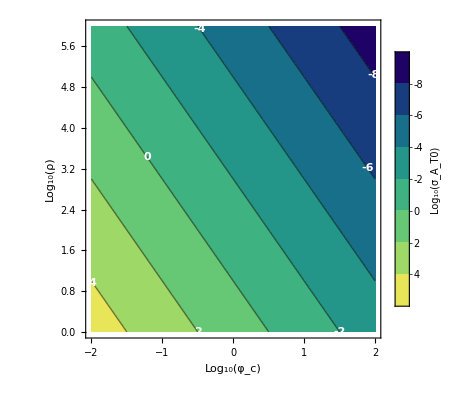

```mathematica
ContourPlot[1-2a-b,{a,-2,2},{b,0,6},FrameLabel->{Subscript[Log, 10][Subscript[φ, c]],Subscript[Log, 10][ρ]},ColorFunction->"BlueGreenYellow",PlotLegends->BarLegend[Automatic,LegendLabel->Subscript[Log, 10][Subscript[σ, Subscript[A, T0]]],LegendLayout->"ReversedColumn"],ContourLabels->Function[{a,b,c},Text[Style[c,White,Bold,Medium],{a,b}]]]
```

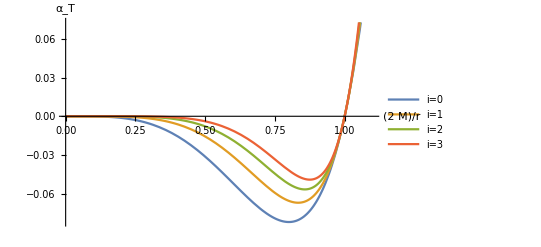

```mathematica
aTi[x_]:=-n^2(1-x)x^(i+2n+2)
Plot[{aTi[x]/.{i->0,n->1},aTi[x]/.{i->1,n->1},aTi[x]/.{i->2,n->1},aTi[x]/.{i->3,n->1}},{x,0,1.1},PlotLegends->{"i=0","i=1","i=2","i=3"},AxesLabel->{(2M/r),Subscript[α, T]}]
```

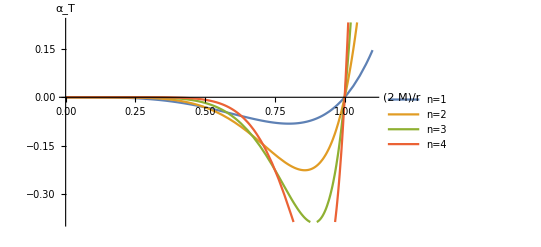

```mathematica
aT[x_]:=-n^2(1-x)x^(2n+2)
Plot[{aT[x]/.n->1,aT[x]/.n->2,aT[x]/.n->3,aT[x]/.n->4},{x,0,1.1},PlotLegends->{"n=1","n=2","n=3","n=4"},AxesLabel->{(2M/r),Subscript[α, T]}]
```